# NQCayleyGraph.nb

This program takes a presentation for an N-quandle and outputs the size and Cayley graph, if the N-quandle is finite, using Winker’s algorithm.  The input is the generators, the initial relations, and the secondary relations (including the N-quandle relations).

For example, the input data to compute the 3-quandle of the trefoil knot is (the output is shown below the code):

Generators={a,b};
Initial={{a,b,a,b},{b,a,b,a}};
Relations={{a,a,a},{b,b,b},{a,b,a,-b,-a,-b}}; 

The initial relations are (a*b)*a = b and (b*a)*b = a, where * is the quandle operation.
The secondary relations are ((x*a)*a)*a = x, ((x*b)*b)*b = x and (((((x*a)*b)*a)**b)**a)**b = x, where x is any element of the quandle (here ** represents the inverse quandle operation, so (x*a)**a = x). Note that for the secondary relations, we do not include the arbitrary ‘x’.

Note: choose the generators and initial relations so they do not include the inverse quandle operation.

```mathematica
GetVertices[E_]:=Select[Union[Flatten[E]],IntegerQ]
```

```mathematica
GetGenerators[E_]:=Complement[Union[Flatten[E]],GetVertices[E]]
```

```mathematica
(* This procedure collapses the graph by looking for multiple edges with the same label incident to a single vertex, and merging them *)
Collapse[edges_]:=Module[{i=1,j=1,temp,x,y,k,done=False,E=edges,V,G,M,v,g,m,p,pos1,pos2,R},
While[!done,
done=True;

(*rewrite edges so lower vertex is always first, reversing the generator if needed*)
For[i=1,i≤Length[E],i++,
If[E[[i]][[1]]>E[[i]][[2]],
temp=E[[i]][[1]];
E[[i]][[1]]=E[[i]][[2]];
E[[i]][[2]]=temp;
E[[i]][[3]]=-E[[i]][[3]]];
];

M={};
V=GetVertices[E];
v=Length[V];
G=GetGenerators[E];
g=Length[G];

For[i=1,i≤v,i++,
For[j=1,j≤g,j++,
AppendTo[M,Count[E,{V[[i]],_,G[[j]]}|{_,V[[i]],-G[[j]]}]-Min[Count[E,{V[[i]],V[[i]],G[[j]]}],Count[E,{V[[i]],V[[i]],-G[[j]]}]]]]];
m=Max[M];
If[m>1, (* if a vertex has multiple edges with the same label *)
p=Position[M,m,1,1][[1]][[1]];
x=Mod[p-1,g]+1;
y=Quotient[p-1,g]+1;
pos1=Position[E,{V[[y]],_,G[[x]]}];
pos2=Position[E,{_,V[[y]],-G[[x]]}];
R=Union[Extract[E,pos1][[1;;Length[pos1],2]],Extract[E,pos2][[1;;Length[pos2],1]]];
For[k=2,k≤m,k++,
E=E/.R[[k]]->R[[1]]];
E=Union[E];(* remove repeats *)
done=False];
];
E]
```

```mathematica
(*Add directed cycle at vertex for each relation*)
AddRelations[edges_,vertex_,Relations_]:=Module[{E=edges,V,next,i,j},
For[j=1,j<=Length[Relations],j++,
V=GetVertices[E];
next=V[[Length[V]]]+1;
AppendTo[E,{vertex,next,Relations[[j]][[1]]}];
For[i=2,i<Length[Relations[[j]]],i++,
AppendTo[E,{next+i-2,next+i-1,Relations[[j]][[i]]}]];
AppendTo[E,{next+i-2,vertex,Relations[[j]][[Length[Relations[[j]]]]]}];
E=Collapse[E]];
E]
```

```mathematica
QGraph[Relations_,Generators_,Initial_]:=Module[{E={}, CV={},V,done=False,next,i=1,j,g,init,nextvertex},
(* Initialization *)
init=Initial;
(* Add vertices and loops for each generator *)
For[g=1,g≤Length[Generators],g++,
AppendTo[E,{g,g,Generators[[g]]}];
AppendTo[E,{g,g,-Generators[[g]]}];
init=init/.Generators[[g]]->g];

(*Problem: if initial relations have negative generators (triangle inverse), then the Generators[[init[[i]][[2]]]] does not work properly*)

(* Add initial relations *)
For[i=1,i≤Length[init],i++,
If[Length[init[[i]]]==3,AppendTo[E,{init[[i]][[1]],init[[i]][[3]],Sign[init[[i]][[2]]]*Generators[[Abs[init[[i]][[2]]]]]}],nextvertex=Length[GetVertices[E]]+1;
AppendTo[E,{init[[i]][[1]],nextvertex,Sign[init[[i]][[2]]]*Generators[[Abs[init[[i]][[2]]]]]}];
For[j=1,j≤Length[init[[i]]]-4,j++,
AppendTo[E,{nextvertex+j-1,nextvertex+j,Sign[init[[i]][[j+2]]]*Generators[[Abs[init[[i]][[j+2]]]]]}]];
AppendTo[E,{nextvertex+Length[init[[i]]]-4,init[[i]][[Length[init[[i]]]]],Sign[init[[i]][[Length[init[[i]]]-1]]]*Generators[[Abs[init[[i]][[Length[init[[i]]]-1]]]]]}]]];

(*Print[MakeGraph[E]]; - used for debugging*)

(*add other relations*)
i=1;
E=AddRelations[E,1,Relations];
CV=Sort[Append[CV,1]]; (*CV is the set of completed vertices, where all relations have been added and collapsed*)
(*Print[MakeGraph[E]]; (*Check initialization*)*)

(*done when all vertices are completed*)
done=(CV==GetVertices[E]);
While[!done,
(*Print[GraphPlot[MakeGraph[E]]];*)
(*Print[Length[E]];*)
next=Complement[GetVertices[E],CV][[1]];
E=AddRelations[E,next,Relations];
V=GetVertices[E];
CV=Sort[Append[CV,next]];
(*throw away completed vertices that were collapsed*)
CV=Intersection[CV,V];
(*Print[MakeGraph[E]];*)
If[Length[CV]>(50*i),Print[TimeUsed[],"*",Length[GetVertices[E]],"*",Length[CV]];i++]; (* provide some output to track progress of program *)
done=((CV==V)||(Length[CV]>10000))];
Print[Length[GetVertices[E]],"*",Length[CV]];
E]
```

```mathematica
MakeGraph[edges_]:=Module[{i,G},
G={};
For[i=1,i≤Length[edges],i++,G=Append[G,{edges[[i]][[1]]->edges[[i]][[2]],edges[[i]][[3]]}]];
G]
```

## Q3(trefoil)

```mathematica
Generators={a,b};
Initial={{a,b,a,b},{b,a,b,a}};
Relations={{a,a,a},{b,b,b},{a,b,a,-b,-a,-b}}; 
(* x^relation = x *)
```

Part::partw: Part 2 of {3} does not exist.

Part::partw: Part 2 of {4} does not exist.

Part::partw: Part 2 of {3} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

4*4

{{1,1,-a},{1,1,a},{1,3,b},{1,4,-b},{2,2,-b},{2,2,b},{2,3,-a},{2,4,a},{3,4,-a},{3,4,b}}

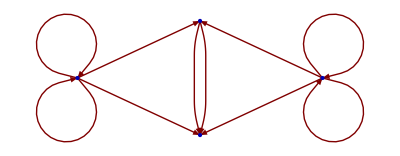

```mathematica
G=QGraph[Relations,Generators,Initial]
GraphPlot[MakeGraph[G]]
```

## Triple Link (T_3,3)

## Q(2,3,3)

```mathematica
Generators={a,b,c};
Initial={{a,c,b,a},{c,b,a,c},{b,a,c,b}};
Relations={{a,a},{b,b,b},{c,c,c},{-a,-b,-c,a,c,b},{-c,-a,-b,c,b,a}}; 
(* x^relation = x  *)
```

Part::partw: Part 2 of {4} does not exist.

Part::partw: Part 2 of {6} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

14*14

{{1,1,-a},{1,1,a},{1,4,-b},{1,4,c},{1,7,b},{1,9,-c},{2,2,-b},{2,2,b},{2,6,-a},{2,6,a},{2,6,-c},{2,10,c},{3,3,-c},{3,3,c},{3,5,-a},{3,5,a},{3,5,b},{3,12,-b},{4,7,-b},{4,9,c},{4,13,-a},{4,13,a},{5,12,b},{5,12,c},{5,15,-c},{6,10,-b},{6,10,-c},{6,16,b},{7,9,-a},{7,9,a},{7,13,-c},{7,17,c},{9,13,b},{9,17,-b},{10,16,-a},{10,16,a},{10,16,-b},{12,15,-a},{12,15,a},{12,15,c},{13,17,b},{13,17,-c},{15,15,-b},{15,15,b},{16,16,-c},{16,16,c},{17,17,-a},{17,17,a}}

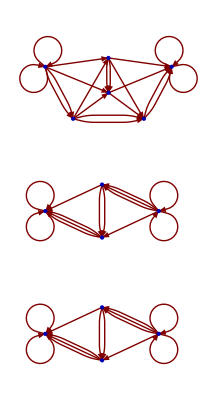

```mathematica
G=QGraph[Relations,Generators,Initial]
GraphPlot[MakeGraph[G]]
```

## Q(2,3,4)

```mathematica
Generators={a,b,c};
Initial={{a,c,b,a},{c,b,a,c},{b,a,c,b}};
Relations={{a,a},{b,b,b},{c,c,c,c},{-a,-b,-c,a,c,b},{-c,-a,-b,c,b,a}}; 
(* x^relation = x  *)
```

Part::partw: Part 2 of {4} does not exist.

Part::partw: Part 2 of {6} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

26*26

{{1,1,-a},{1,1,a},{1,4,-b},{1,4,c},{1,7,b},{1,10,-c},{2,2,-b},{2,2,b},{2,6,-a},{2,6,a},{2,6,-c},{2,11,c},{3,3,-c},{3,3,c},{3,5,-a},{3,5,a},{3,5,b},{3,14,-b},{4,7,-b},{4,9,c},{4,15,-a},{4,15,a},{5,14,b},{5,14,c},{5,18,-c},{6,11,-b},{6,12,-c},{6,19,b},{7,10,-a},{7,10,a},{7,15,-c},{7,20,c},{9,10,c},{9,15,b},{9,22,-a},{9,22,a},{9,24,-b},{10,20,-b},{10,22,b},{11,12,c},{11,19,-b},{11,25,-a},{11,25,a},{12,19,-a},{12,19,a},{12,25,b},{12,27,-b},{14,17,c},{14,18,-a},{14,18,a},{15,21,-c},{15,24,b},{17,18,b},{17,18,c},{17,28,-a},{17,28,a},{17,28,-b},{18,28,b},{19,25,-c},{19,27,c},{20,21,c},{20,22,-b},{20,31,-a},{20,31,a},{21,24,-a},{21,24,a},{21,31,b},{21,33,-b},{22,24,c},{22,31,-c},{24,33,c},{25,27,b},{25,30,-c},{27,30,-a},{27,30,a},{27,30,c},{28,28,-c},{28,28,c},{30,30,-b},{30,30,b},{31,33,b},{31,33,-c},{33,33,-a},{33,33,a}}

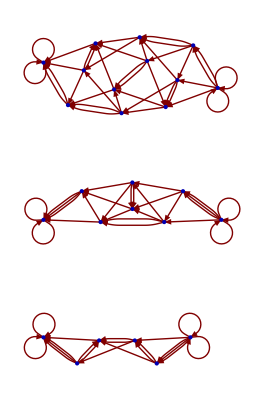

```mathematica
G=QGraph[Relations,Generators,Initial]
GraphPlot[MakeGraph[G]]
```

## Q(2,3,5)

```mathematica
Generators={a,b,c};
Initial={{a,c,b,a},{c,b,a,c},{b,a,c,b}};
Relations={{a,a},{b,b,b},{c,c,c,c,c},{-a,-b,-c,a,c,b},{-c,-a,-b,c,b,a}}; 
(* x^relation = x  *)
```

Part::partw: Part 2 of {4} does not exist.

Part::partw: Part 2 of {6} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

17.7563*61*51

62*62

{{1,1,-a},{1,1,a},{1,4,-b},{1,4,c},{1,7,b},{1,11,-c},{2,2,-b},{2,2,b},{2,6,-a},{2,6,a},{2,6,-c},{2,12,c},{3,3,-c},{3,3,c},{3,5,-a},{3,5,a},{3,5,b},{3,16,-b},{4,7,-b},{4,9,c},{4,17,-a},{4,17,a},{5,16,b},{5,16,c},{5,21,-c},{6,12,-b},{6,14,-c},{6,22,b},{7,11,-a},{7,11,a},{7,17,-c},{7,23,c},{9,10,c},{9,17,b},{9,26,-a},{9,26,a},{9,28,-b},{10,11,c},{10,26,b},{10,29,-a},{10,29,a},{10,31,-b},{11,23,-b},{11,29,b},{12,13,c},{12,22,-b},{12,32,-a},{12,32,a},{13,14,c},{13,32,b},{13,33,-a},{13,33,a},{13,35,-b},{14,22,-a},{14,22,a},{14,33,b},{14,37,-b},{16,19,c},{16,21,-a},{16,21,a},{17,25,-c},{17,28,b},{19,20,c},{19,21,b},{19,38,-a},{19,38,a},{19,40,-b},{20,21,c},{20,38,b},{20,40,-a},{20,40,a},{20,43,-b},{21,40,b},{22,32,-c},{22,37,c},{23,24,c},{23,29,-b},{23,47,-a},{23,47,a},{24,25,c},{24,47,b},{24,48,-a},{24,48,a},{24,50,-b},{25,28,-a},{25,28,a},{25,48,b},{25,52,-b},{26,28,c},{26,31,b},{26,56,-c},{28,52,c},{29,31,c},{29,47,-c},{31,56,-a},{31,56,a},{31,58,c},{32,35,b},{32,46,-c},{33,35,c},{33,37,b},{33,63,-c},{35,46,-a},{35,46,a},{35,61,c},{37,45,c},{37,63,-a},{37,63,a},{38,40,c},{38,43,b},{38,67,-c},{40,43,c},{43,66,c},{43,67,-a},{43,67,a},{45,46,c},{45,63,b},{45,68,-a},{45,68,a},{45,70,-b},{46,61,-b},{46,68,b},{47,50,b},{47,59,-c},{48,50,c},{48,52,b},{48,74,-c},{50,59,-a},{50,59,a},{50,72,c},{52,55,c},{52,74,-a},{52,74,a},{55,56,c},{55,74,b},{55,75,-a},{55,75,a},{55,77,-b},{56,58,-b},{56,75,b},{58,59,c},{58,75,-b},{58,78,-a},{58,78,a},{59,72,-b},{59,78,b},{61,62,c},{61,68,-b},{61,79,-a},{61,79,a},{62,63,c},{62,70,-a},{62,70,a},{62,79,b},{62,82,-b},{63,70,b},{66,67,b},{66,67,c},{66,83,-a},{66,83,a},{66,83,-b},{67,83,b},{68,70,c},{68,79,-c},{70,82,c},{72,73,c},{72,78,-b},{72,87,-a},{72,87,a},{73,74,c},{73,77,-a},{73,77,a},{73,87,b},{73,90,-b},{74,77,b},{75,77,c},{75,78,-c},{77,90,c},{78,87,-c},{79,82,b},{79,86,-c},{82,86,-a},{82,86,a},{82,86,c},{83,83,-c},{83,83,c},{86,86,-b},{86,86,b},{87,90,b},{87,90,-c},{90,90,-a},{90,90,a}}

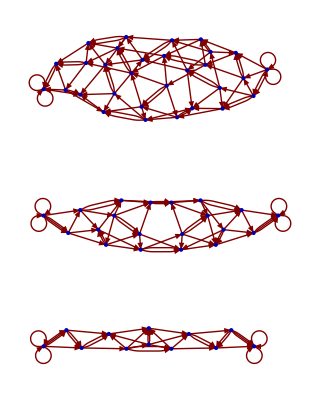

```mathematica
G=QGraph[Relations,Generators,Initial]
GraphPlot[MakeGraph[G]]
```

## Triple Link (T_2,4 with axis)

## Q(2,3,2)

```mathematica
Generators={a,b,c};
Initial={{a,b,a,b,c,a},{c,a,b,c},{b,a,b,a,b,c,b}};
Relations={{a,a},{b,b,b},{c,c},{-c,-b,-a,c,a,b},{-a,-c,-b,-a,-b,a,b,a,b,c},{-b,-c,-b,-a,-b,-a,b,a,b,a,b,c}}; 
(* x^relation = x  *)
```

Part::partw: Part 2 of {5} does not exist.

Part::partw: Part 2 of {4} does not exist.

Part::partw: Part 2 of {5} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

26*26

{{1,1,-a},{1,1,a},{1,4,b},{1,6,-c},{1,6,c},{1,13,-b},{2,2,-b},{2,2,b},{2,8,-a},{2,8,a},{2,11,-c},{2,11,c},{3,3,-c},{3,3,c},{3,7,-a},{3,7,a},{3,7,-b},{3,23,b},{4,5,-a},{4,5,a},{4,13,b},{4,17,-c},{4,17,c},{5,6,b},{5,21,-c},{5,21,c},{5,30,-b},{6,28,-a},{6,28,a},{6,30,b},{7,23,-b},{7,25,-c},{7,25,c},{8,9,b},{8,9,-c},{8,9,c},{8,48,-b},{9,10,-a},{9,10,a},{9,48,b},{10,11,b},{10,52,-b},{10,52,-c},{10,52,c},{11,48,-a},{11,48,a},{11,52,b},{13,17,-a},{13,17,a},{13,19,-c},{13,19,c},{17,21,b},{17,28,-b},{19,20,-b},{19,30,-a},{19,30,a},{19,37,b},{20,21,-a},{20,21,a},{20,30,-c},{20,30,c},{20,37,-b},{21,28,b},{23,26,-a},{23,26,a},{23,26,-c},{23,26,c},{25,26,-b},{25,46,-a},{25,46,a},{25,46,b},{26,46,-b},{28,37,-c},{28,37,c},{37,37,-a},{37,37,a},{46,46,-c},{46,46,c},{48,50,-c},{48,50,c},{50,50,-b},{50,50,b},{50,52,-a},{50,52,a}}

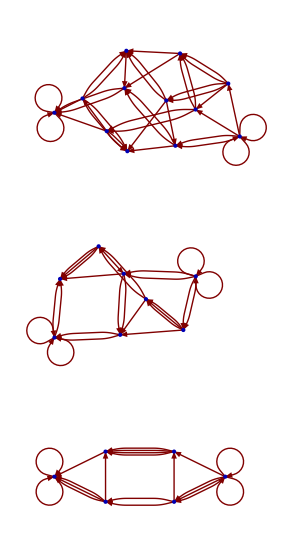

```mathematica
G=QGraph[Relations,Generators,Initial]
GraphPlot[MakeGraph[G]]
```

## Torus Links (T_2,n), n = 4, 6, 8, 10

## Q(3,3)(T_2,4)

```mathematica
Generators={a,b};
Initial={{a,b,a,b,a},{b,a,b,a,b}};
Relations={{a,a,a},{b,b,b},{-a,-b,-a,-b,a,b,a,b}}; 
(* x^relation = x  *)
```

Part::partw: Part 2 of {3} does not exist.

Part::partw: Part 2 of {5} does not exist.

Part::partw: Part 2 of {4} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

8*8

{{1,1,-a},{1,1,a},{1,3,b},{1,4,-b},{2,2,-b},{2,2,b},{2,5,a},{2,6,-a},{3,4,a},{3,4,b},{3,8,-a},{4,8,a},{5,6,a},{5,6,b},{5,10,-b},{6,10,b},{8,8,-b},{8,8,b},{10,10,-a},{10,10,a}}

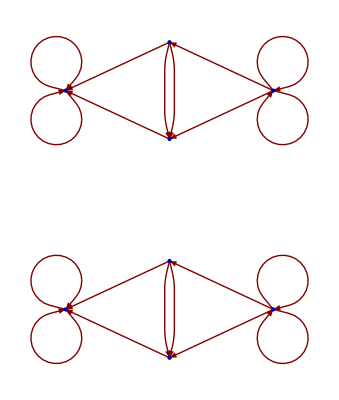

```mathematica
G=QGraph[Relations,Generators,Initial]
GraphPlot[MakeGraph[G]]
```

## Q(3,4)(T_2,4)

```mathematica
Generators={a,b};
Initial={{a,b,a,b,a},{b,a,b,a,b}};
Relations={{a,a,a},{b,b,b,b},{-a,-b,-a,-b,a,b,a,b}}; 
(* x^relation = x  *)
```

Part::partw: Part 2 of {3} does not exist.

Part::partw: Part 2 of {5} does not exist.

Part::partw: Part 2 of {4} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

14*14

{{1,1,-a},{1,1,a},{1,3,b},{1,4,-b},{2,2,-b},{2,2,b},{2,5,a},{2,6,-a},{3,4,a},{3,8,b},{3,10,-a},{4,8,-b},{4,10,a},{5,6,a},{5,6,b},{5,21,-b},{6,20,b},{8,12,a},{8,18,-a},{10,12,-b},{10,18,b},{12,18,a},{12,23,-b},{18,23,b},{20,21,a},{20,21,b},{20,25,-a},{21,25,a},{23,23,-a},{23,23,a},{25,25,-b},{25,25,b}}

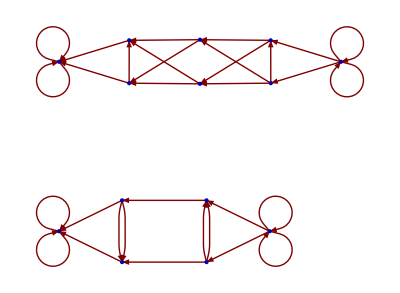

```mathematica
G=QGraph[Relations,Generators,Initial]
GraphPlot[MakeGraph[G]]
```

## Q(3,5)(T_2,4)

```mathematica
Generators={a,b};
Initial={{a,b,a,b,a},{b,a,b,a,b}};
Relations={{a,a,a},{b,b,b,b,b},{-a,-b,-a,-b,a,b,a,b}}; 
(* x^relation = x  *)
```

Part::partw: Part 2 of {3} does not exist.

Part::partw: Part 2 of {5} does not exist.

Part::partw: Part 2 of {4} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

32*32

{{1,1,-a},{1,1,a},{1,3,b},{1,4,-b},{2,2,-b},{2,2,b},{2,5,a},{2,6,-a},{3,4,a},{3,8,b},{3,11,-a},{4,9,-b},{4,11,a},{5,6,a},{5,6,b},{5,23,-b},{6,21,b},{8,9,b},{8,13,a},{8,25,-a},{9,19,-a},{9,27,a},{11,13,-b},{11,19,b},{13,25,a},{13,30,-b},{19,27,-a},{19,29,b},{21,22,b},{21,23,a},{21,40,-a},{22,23,b},{22,42,a},{22,44,-a},{23,40,a},{25,27,-b},{25,36,b},{27,38,-b},{29,30,b},{29,38,a},{29,48,-a},{30,36,-a},{30,50,a},{36,46,b},{36,50,-a},{38,46,-b},{38,48,a},{40,42,-b},{40,44,b},{42,44,a},{42,61,-b},{44,60,b},{46,52,a},{46,58,-a},{48,50,-b},{48,58,b},{50,52,-b},{52,58,a},{52,63,-b},{58,63,b},{60,61,a},{60,61,b},{60,65,-a},{61,65,a},{63,63,-a},{63,63,a},{65,65,-b},{65,65,b}}

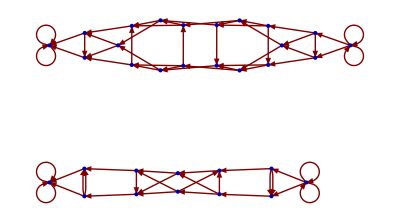

```mathematica
G=QGraph[Relations,Generators,Initial]
GraphPlot[MakeGraph[G]]
```

## Q(2,3)(T_2,6)

```mathematica
Generators={a,b};
Initial={{a,b,a,b,a,b,a},{b,a,b,a,b,a,b}};
Relations={{a,a},{b,b,b},{-a,-b,-a,-b,-a,-b,a,b,a,b,a,b}}; 
(* x^relation = x  *)
```

Part::partw: Part 2 of {3} does not exist.

Part::partw: Part 2 of {7} does not exist.

Part::partw: Part 2 of {6} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

10*10

{{1,1,-a},{1,1,a},{1,3,b},{1,6,-b},{2,2,-b},{2,2,b},{2,7,-a},{2,7,a},{3,4,-a},{3,4,a},{3,6,b},{4,5,b},{4,11,-b},{5,6,-a},{5,6,a},{5,11,b},{7,8,b},{7,9,-b},{8,9,-a},{8,9,a},{8,9,b},{11,11,-a},{11,11,a}}

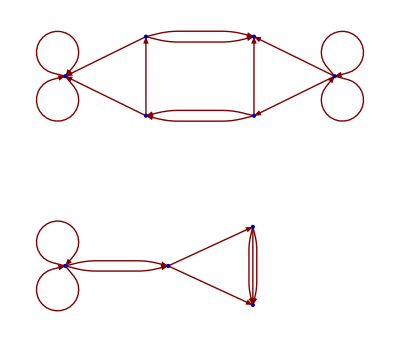

```mathematica
G=QGraph[Relations,Generators,Initial]
GraphPlot[MakeGraph[G]]
```

## Q(2,4)(T_2,6)

```mathematica
Generators={a,b};
Initial={{a,b,a,b,a,b,a},{b,a,b,a,b,a,b}};
Relations={{a,a},{b,b,b,b},{-a,-b,-a,-b,-a,-b,a,b,a,b,a,b}}; 
(* x^relation = x  *)
```

Part::partw: Part 2 of {3} does not exist.

Part::partw: Part 2 of {7} does not exist.

Part::partw: Part 2 of {6} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

18*18

{{1,1,-a},{1,1,a},{1,3,b},{1,6,-b},{2,2,-b},{2,2,b},{2,7,-a},{2,7,a},{3,4,-a},{3,4,a},{3,12,b},{4,5,b},{4,14,-b},{5,6,-a},{5,6,a},{5,18,b},{6,12,-b},{7,8,b},{7,9,-b},{8,9,-a},{8,9,a},{8,24,b},{9,24,-b},{12,16,-a},{12,16,a},{14,15,-a},{14,15,a},{14,18,-b},{15,16,-b},{15,36,b},{16,22,-b},{18,22,-a},{18,22,a},{22,36,-b},{24,27,-a},{24,27,a},{27,27,-b},{27,27,b},{36,36,-a},{36,36,a}}

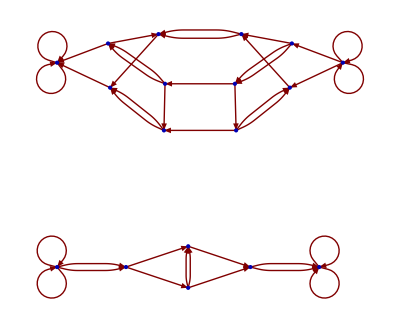

```mathematica
G=QGraph[Relations,Generators,Initial]
GraphPlot[MakeGraph[G]]
```

## Q(2,5)(T_2,6)

```mathematica
Generators={a,b};
Initial={{a,b,a,b,a,b,a},{b,a,b,a,b,a,b}};
Relations={{a,a},{b,b,b,b,b},{-a,-b,-a,-b,-a,-b,a,b,a,b,a,b}}; 
(* x^relation = x  *)
```

Part::partw: Part 2 of {3} does not exist.

Part::partw: Part 2 of {7} does not exist.

Part::partw: Part 2 of {6} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

42*42

{{1,1,-a},{1,1,a},{1,3,b},{1,6,-b},{2,2,-b},{2,2,b},{2,7,-a},{2,7,a},{3,4,-a},{3,4,a},{3,12,b},{4,5,b},{4,15,-b},{5,6,-a},{5,6,a},{5,19,b},{6,13,-b},{7,8,b},{7,9,-b},{8,9,-a},{8,9,a},{8,26,b},{9,27,-b},{12,13,b},{12,17,-a},{12,17,a},{13,23,-a},{13,23,a},{15,16,-a},{15,16,a},{15,20,-b},{16,17,-b},{16,42,b},{17,33,-b},{19,20,b},{19,24,-a},{19,24,a},{20,44,-a},{20,44,a},{23,24,-b},{23,34,b},{24,48,-b},{26,27,b},{26,31,-a},{26,31,a},{27,30,-a},{27,30,a},{30,31,-b},{30,54,b},{31,53,-b},{33,34,-a},{33,34,a},{33,46,-b},{34,51,b},{42,43,-a},{42,43,a},{42,46,b},{43,44,b},{43,68,-b},{44,49,b},{46,66,-a},{46,66,a},{48,49,-a},{48,49,a},{48,51,-b},{49,73,b},{51,65,-a},{51,65,a},{53,54,-a},{53,54,a},{53,56,-b},{54,56,b},{56,91,-a},{56,91,a},{65,66,b},{65,82,-b},{66,69,b},{68,69,-a},{68,69,a},{68,73,-b},{69,94,b},{73,82,-a},{73,82,a},{82,94,-b},{91,91,-b},{91,91,b},{94,94,-a},{94,94,a}}

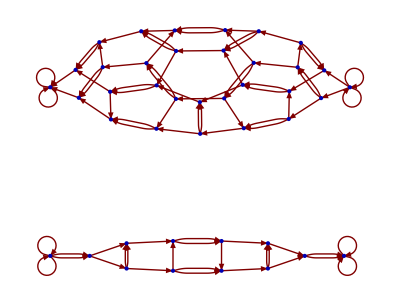

```mathematica
G=QGraph[Relations,Generators,Initial]
GraphPlot[MakeGraph[G]]
```

## Q(2,3)(T_2,8)

```mathematica
Generators={a,b};
Initial={{a,b,a,b,a,b,a,b,a},{b,a,b,a,b,a,b,a,b}};
Relations={{a,a},{b,b,b},{-a,-b,-a,-b,-a,-b,-a,-b,a,b,a,b,a,b,a,b}}; 
(* x^relation = x  *)
```

Part::partw: Part 2 of {3} does not exist.

Part::partw: Part 2 of {9} does not exist.

Part::partw: Part 2 of {8} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

20*20

{{1,1,-a},{1,1,a},{1,3,b},{1,8,-b},{2,2,-b},{2,2,b},{2,9,-a},{2,9,a},{3,4,-a},{3,4,a},{3,8,b},{4,5,b},{4,15,-b},{5,6,-a},{5,6,a},{5,15,b},{6,7,b},{6,18,-b},{7,8,-a},{7,8,a},{7,18,b},{9,10,b},{9,13,-b},{10,11,-a},{10,11,a},{10,13,b},{11,12,b},{11,27,-b},{12,13,-a},{12,13,a},{12,27,b},{15,16,-a},{15,16,a},{16,17,-b},{16,23,b},{17,18,-a},{17,18,a},{17,23,-b},{23,23,-a},{23,23,a},{27,28,-a},{27,28,a},{28,28,-b},{28,28,b}}

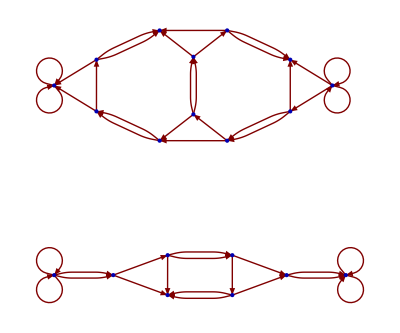

```mathematica
G=QGraph[Relations,Generators,Initial]
GraphPlot[MakeGraph[G]]
```

## Q(2,3)(T_2,10)

```mathematica
Generators={a,b};
Initial={{a,b,a,b,a,b,a,b,a,b,a},{b,a,b,a,b,a,b,a,b,a,b}};
Relations={{a,a},{b,b,b},{-a,-b,-a,-b,-a,-b,-a,-b,-a,-b,a,b,a,b,a,b,a,b,a,b}}; 
(* x^relation = x  *)
```

Part::partw: Part 2 of {3} does not exist.

Part::partw: Part 2 of {11} does not exist.

Part::partw: Part 2 of {10} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

50*50

{{1,1,-a},{1,1,a},{1,3,b},{1,10,-b},{2,2,-b},{2,2,b},{2,11,-a},{2,11,a},{3,4,-a},{3,4,a},{3,10,b},{4,5,b},{4,19,-b},{5,6,-a},{5,6,a},{5,19,b},{6,7,b},{6,27,-b},{7,8,-a},{7,8,a},{7,27,b},{8,9,b},{8,24,-b},{9,10,-a},{9,10,a},{9,24,b},{11,12,b},{11,17,-b},{12,13,-a},{12,13,a},{12,17,b},{13,14,b},{13,43,-b},{14,15,-a},{14,15,a},{14,43,b},{15,16,b},{15,48,-b},{16,17,-a},{16,17,a},{16,48,b},{19,20,-a},{19,20,a},{20,21,-b},{20,32,b},{21,22,-a},{21,22,a},{21,32,-b},{22,23,-b},{22,37,b},{23,24,-a},{23,24,a},{23,37,-b},{27,28,-a},{27,28,a},{28,29,-b},{28,40,b},{29,30,-a},{29,30,a},{29,40,-b},{30,31,-b},{30,74,b},{31,32,-a},{31,32,a},{31,74,-b},{37,38,-a},{37,38,a},{38,39,-b},{38,71,b},{39,40,-a},{39,40,a},{39,71,-b},{43,44,-a},{43,44,a},{44,45,-b},{44,56,b},{45,46,-a},{45,46,a},{45,56,-b},{46,47,-b},{46,53,b},{47,48,-a},{47,48,a},{47,53,-b},{53,54,-a},{53,54,a},{54,55,-b},{54,105,b},{55,56,-a},{55,56,a},{55,105,-b},{71,72,-a},{71,72,a},{72,73,b},{72,89,-b},{73,74,-a},{73,74,a},{73,89,b},{89,89,-a},{89,89,a},{105,106,-a},{105,106,a},{106,106,-b},{106,106,b}}

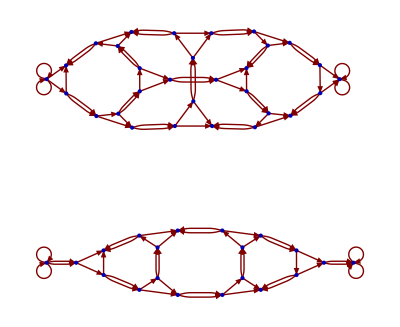

```mathematica
G=QGraph[Relations,Generators,Initial]
GraphPlot[MakeGraph[G]]
```

{{19,15,1},{52,51,1},{80,34,3},{40,39,2},{9,79,2},{22,23,1},{4,1,2},{52,41,2},{12,36,3},{80,79,1},{21,20,1},{40,41,1},{51,3,2},{32,38,3},{53,24,2},{6,7,1},{10,11,1},{9,8,1},{37,2,3},{10,9,3},{38,37,2},{37,36,1},{2,2,2},{79,35,3},{36,12,3},{9,10,3},{5,4,1},{22,165,2},{15,19,1},{52,53,3},{22,21,3},{80,80,2},{20,19,2},{23,22,1},{21,32,2},{1,24,3},{39,40,2},{3,16,1},{23,10,2},{4,5,1},{3,3,3},{165,22,2},{10,23,2},{2,37,3},{8,7,2},{41,7,3},{7,6,1},{11,10,1},{6,5,2},{1,4,2},{33,39,3},{36,35,2},{11,8,3},{35,34,1},{8,9,1},{19,4,3},{20,23,3},{34,35,1},{24,24,1},{79,80,1},{39,33,3},{51,52,1},{53,52,3},{32,33,1},{15,16,2},{5,15,3},{32,21,2},{16,3,1},{7,8,2},{33,34,2},{37,38,2},{38,32,3},{24,53,2},{40,6,3},{23,20,3},{2,12,1},{53,165,1},{35,36,2},{1,1,1},{20,21,1},{6,40,3},{15,5,3},{12,11,2},{5,6,2},{24,1,3},{35,79,3},{16,16,3},{165,53,1},{34,80,3},{38,39,1},{79,9,2},{165,51,3},{12,2,1},{19,20,2},{7,41,3},{3,51,2},{51,165,3},{36,37,1},{4,19,3},{41,40,1},{21,22,3},{11,12,2},{39,38,1},{34,33,2},{41,52,2},{8,11,3},{33,32,1},{16,15,2}}

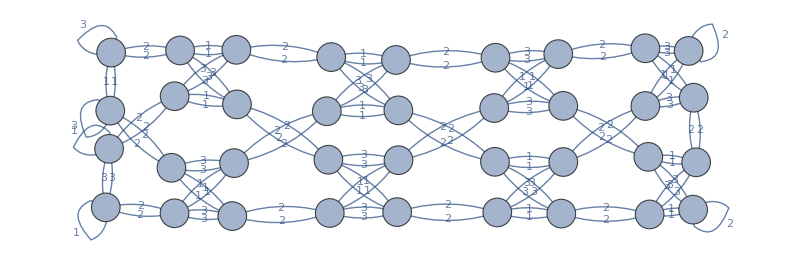

```mathematica
G={{19,15,1},{52,51,1},{80,34,3},{40,39,2},{9,79,2},{22,23,1},{4,1,2},{52,41,2},{12,36,3},{80,79,1},{21,20,1},{40,41,1},{51,3,2},{32,38,3},{53,24,2},{6,7,1},{10,11,1},{9,8,1},{37,2,3},{10,9,3},{38,37,2},{37,36,1},{2,2,2},{79,35,3},{36,12,3},{9,10,3},{5,4,1},{22,165,2},{15,19,1},{52,53,3},{22,21,3},{80,80,2},{20,19,2},{23,22,1},{21,32,2},{1,24,3},{39,40,2},{3,16,1},{23,10,2},{4,5,1},{3,3,3},{165,22,2},{10,23,2},{2,37,3},{8,7,2},{41,7,3},{7,6,1},{11,10,1},{6,5,2},{1,4,2},{33,39,3},{36,35,2},{11,8,3},{35,34,1},{8,9,1},{19,4,3},{20,23,3},{34,35,1},{24,24,1},{79,80,1},{39,33,3},{51,52,1},{53,52,3},{32,33,1},{15,16,2},{5,15,3},{32,21,2},{16,3,1},{7,8,2},{33,34,2},{37,38,2},{38,32,3},{24,53,2},{40,6,3},{23,20,3},{2,12,1},{53,165,1},{35,36,2},{1,1,1},{20,21,1},{6,40,3},{15,5,3},{12,11,2},{5,6,2},{24,1,3},{35,79,3},{16,16,3},{165,53,1},{34,80,3},{38,39,1},{79,9,2},{165,51,3},{12,2,1},{19,20,2},{7,41,3},{3,51,2},{51,165,3},{36,37,1},{4,19,3},{41,40,1},{21,22,3},{11,12,2},{39,38,1},{34,33,2},{41,52,2},{8,11,3},{33,32,1},{16,15,2}}
GraphPlot[MakeGraph[G], VertexLabels->Placed[Automatic,Center],VertexSize->.75]
```

```mathematica
{{19,15,1},{52,51,1},{80,34,3},{40,39,2},{9,79,2},{22,23,1},{4,1,2},{52,41,2},{12,36,3},{80,79,1},{21,20,1},{40,41,1},{51,3,2},{32,38,3},{53,24,2},{6,7,1},{10,11,1},{9,8,1},{37,2,3},{10,9,3},{38,37,2},{37,36,1},{2,2,2},{79,35,3},{36,12,3},{9,10,3},{5,4,1},{22,165,2},{15,19,1},{52,53,3},{22,21,3},{80,80,2},{20,19,2},{23,22,1},{21,32,2},{1,24,3},{39,40,2},{3,16,1},{23,10,2},{4,5,1},{3,3,3},{165,22,2},{10,23,2},{2,37,3},{8,7,2},{41,7,3},{7,6,1},{11,10,1},{6,5,2},{1,4,2},{33,39,3},{36,35,2},{11,8,3},{35,34,1},{8,9,1},{19,4,3},{20,23,3},{34,35,1},{24,24,1},{79,80,1},{39,33,3},{51,52,1},{53,52,3},{32,33,1},{15,16,2},{5,15,3},{32,21,2},{16,3,1},{7,8,2},{33,34,2},{37,38,2},{38,32,3},{24,53,2},{40,6,3},{23,20,3},{2,12,1},{53,165,1},{35,36,2},{1,1,1},{20,21,1},{6,40,3},{15,5,3},{12,11,2},{5,6,2},{24,1,3},{35,79,3},{16,16,3},{165,53,1},{34,80,3},{38,39,1},{79,9,2},{165,51,3},{12,2,1},{19,20,2},{7,41,3},{3,51,2},{51,165,3},{36,37,1},{4,19,3},{41,40,1},{21,22,3},{11,12,2},{39,38,1},{34,33,2},{41,52,2},{8,11,3},{33,32,1},{16,15,2}}
```

{{19,15,1},{52,51,1},{80,34,3},{40,39,2},{9,79,2},{22,23,1},{4,1,2},{52,41,2},{12,36,3},{80,79,1},{21,20,1},{40,41,1},{51,3,2},{32,38,3},{53,24,2},{6,7,1},{10,11,1},{9,8,1},{37,2,3},{10,9,3},{38,37,2},{37,36,1},{2,2,2},{79,35,3},{36,12,3},{9,10,3},{5,4,1},{22,165,2},{15,19,1},{52,53,3},{22,21,3},{80,80,2},{20,19,2},{23,22,1},{21,32,2},{1,24,3},{39,40,2},{3,16,1},{23,10,2},{4,5,1},{3,3,3},{165,22,2},{10,23,2},{2,37,3},{8,7,2},{41,7,3},{7,6,1},{11,10,1},{6,5,2},{1,4,2},{33,39,3},{36,35,2},{11,8,3},{35,34,1},{8,9,1},{19,4,3},{20,23,3},{34,35,1},{24,24,1},{79,80,1},{39,33,3},{51,52,1},{53,52,3},{32,33,1},{15,16,2},{5,15,3},{32,21,2},{16,3,1},{7,8,2},{33,34,2},{37,38,2},{38,32,3},{24,53,2},{40,6,3},{23,20,3},{2,12,1},{53,165,1},{35,36,2},{1,1,1},{20,21,1},{6,40,3},{15,5,3},{12,11,2},{5,6,2},{24,1,3},{35,79,3},{16,16,3},{165,53,1},{34,80,3},{38,39,1},{79,9,2},{165,51,3},{12,2,1},{19,20,2},{7,41,3},{3,51,2},{51,165,3},{36,37,1},{4,19,3},{41,40,1},{21,22,3},{11,12,2},{39,38,1},{34,33,2},{41,52,2},{8,11,3},{33,32,1},{16,15,2}}

{{390,30,60},{143,142,2},{23,2,3},{40,39,2},{61,60,1},{178,177,2},{39,38,3},{22,23,1},{135,136,3},{97,98,1},{406,407,2},{41,42,2},{21,20,1},{20,177,3},{76,77,1},{210,211,2},{101,42,1},{409,408,2},{55,54,1},{75,74,1},{127,135,2},{74,73,2},{89,43,1},{192,191,1},{346,74,3},{129,304,3},{205,206,1},{137,137,1},{2,18,1},{52,292,2},{5,4,1},{74,346,3},{15,13,3},{178,179,1},{142,141,1},{252,253,2},{3,3,3},{135,250,1},{11,10,1},{77,16,3},{130,407,3},{53,52,1},{209,208,2},{204,406,1},{347,346,2},{64,63,2},{77,410,2},{13,12,1},{62,99,3},{177,20,3},{67,66,1},{60,61,1},{21,40,3},{180,179,2},{250,135,1},{409,410,1},{20,21,1},{75,250,3},{408,409,2},{101,409,3},{189,190,1},{89,72,3},{76,76,3},{68,49,3},{74,75,1},{208,209,2},{251,252,1},{204,17,3},{66,67,1},{17,16,1},{140,48,3},{292,52,2},{60,18,3},{205,204,2},{47,24,1},{64,65,1},{66,54,3},{22,21,2},{292,44,3},{99,100,1},{177,355,1},{63,62,1},{62,61,2},{347,356,1},{16,17,1},{68,67,2},{191,190,2},{52,51,3},{51,50,1},{12,38,2},{10,11,1},{12,11,3},{39,188,1},{44,38,1},{98,209,3},{179,180,2},{24,97,2},{207,55,3},{24,47,1},{356,355,2},{130,129,1},{42,101,1},{98,99,2},{177,178,2},{141,142,1},{18,17,2},{206,189,3},{54,66,3},{11,12,3},{72,89,3},{19,127,3},{20,19,2},{188,347,3},{189,188,2},{141,100,3},{1,24,3},{292,180,1},{409,101,3},{191,192,1},{304,144,2},{65,410,3},{66,65,2},{23,212,2},{7,6,1},{6,5,2},{8,9,1},{211,128,3},{410,409,1},{73,74,2},{62,63,1},{73,47,3},{15,56,1},{99,98,2},{210,209,1},{60,89,2},{250,251,2},{137,191,3},{50,406,3},{49,68,3},{356,347,1},{251,250,2},{48,140,3},{64,190,3},{10,9,2},{48,49,1},{2,23,3},{204,205,2},{128,127,1},{304,346,1},{19,20,2},{252,178,3},{136,137,2},{38,39,3},{68,111,1},{56,55,2},{100,101,2},{178,252,3},{190,191,2},{51,52,3},{67,22,3},{141,140,2},{16,15,2},{144,7,3},{127,128,1},{408,179,3},{12,13,1},{304,129,3},{112,111,2},{346,347,2},{3,19,1},{129,130,1},{43,89,1},{65,66,2},{6,7,1},{42,43,3},{140,141,2},{5,61,3},{9,8,1},{407,130,3},{112,8,3},{208,251,3},{17,18,2},{253,205,3},{52,53,1},{410,77,2},{189,206,3},{212,23,2},{137,136,2},{408,407,1},{111,112,2},{111,142,3},{17,204,3},{128,211,3},{19,3,1},{188,189,2},{142,111,3},{56,4,3},{251,208,3},{49,48,1},{48,47,2},{63,356,3},{7,144,3},{50,51,1},{8,7,2},{11,192,2},{209,98,3},{136,135,3},{21,22,2},{355,177,1},{98,97,1},{130,130,2},{55,56,2},{190,64,3},{250,75,3},{75,76,2},{54,53,2},{15,16,2},{61,5,3},{206,205,1},{7,8,2},{406,204,1},{179,408,3},{191,137,3},{1,1,1},{207,208,1},{61,62,2},{5,6,2},{410,65,3},{1,13,2},{4,3,2},{97,24,2},{77,76,1},{211,210,2},{47,48,2},{41,40,1},{97,355,3},{355,97,3},{6,192,3},{54,55,1},{73,72,1},{128,129,2},{72,51,2},{129,128,2},{44,43,2},{212,211,1},{43,42,3},{140,136,1},{18,60,3},{192,11,2},{13,15,3},{55,207,3},{355,356,2},{9,212,3},{67,68,2},{144,304,2},{40,41,1},{99,62,3},{111,68,1},{142,143,2},{135,127,2},{143,41,3},{22,67,3},{4,56,3},{407,406,2},{211,212,1},{180,292,1},{53,210,3},{190,189,1},{47,73,3},{38,44,1},{252,251,1},{346,304,1},{2,2,2},{188,39,1},{53,54,2},{41,143,3},{112,253,1},{192,6,3},{143,144,1},{356,63,3},{100,141,3},{208,207,1},{50,49,2},{23,22,1},{39,40,2},{42,41,2},{4,5,1},{3,4,2},{89,60,2},{210,53,3},{76,75,2},{8,112,3},{205,253,3},{100,99,1},{179,178,1},{253,112,1},{56,15,1},{38,12,2},{406,50,3},{407,408,1},{49,50,2},{18,2,1},{16,77,3},{44,292,3},{9,10,2},{207,206,2},{136,140,1},{43,44,2},{65,64,1},{144,143,1},{63,64,2},{127,19,3},{40,21,3},{24,1,3},{253,252,2},{10,180,3},{212,9,3},{51,72,2},{72,73,1},{206,207,2},{180,10,3},{101,100,2},{347,188,3},{209,210,1}}

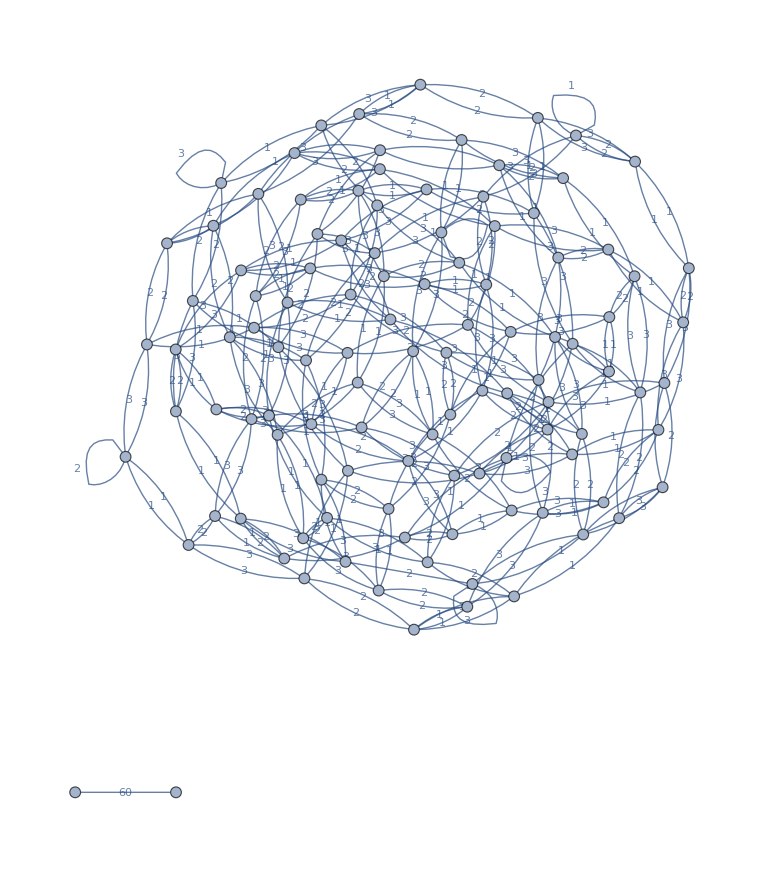

```mathematica
G = {{13,1,2}30,{143,142,2},{23,2,3},{40,39,2},{61,60,1},{178,177,2},{39,38,3},{22,23,1},{135,136,3},{97,98,1},{406,407,2},{41,42,2},{21,20,1},{20,177,3},{76,77,1},{210,211,2},{101,42,1},{409,408,2},{55,54,1},{75,74,1},{127,135,2},{74,73,2},{89,43,1},{192,191,1},{346,74,3},{129,304,3},{205,206,1},{137,137,1},{2,18,1},{52,292,2},{5,4,1},{74,346,3},{15,13,3},{178,179,1},{142,141,1},{252,253,2},{3,3,3},{135,250,1},{11,10,1},{77,16,3},{130,407,3},{53,52,1},{209,208,2},{204,406,1},{347,346,2},{64,63,2},{77,410,2},{13,12,1},{62,99,3},{177,20,3},{67,66,1},{60,61,1},{21,40,3},{180,179,2},{250,135,1},{409,410,1},{20,21,1},{75,250,3},{408,409,2},{101,409,3},{189,190,1},{89,72,3},{76,76,3},{68,49,3},{74,75,1},{208,209,2},{251,252,1},{204,17,3},{66,67,1},{17,16,1},{140,48,3},{292,52,2},{60,18,3},{205,204,2},{47,24,1},{64,65,1},{66,54,3},{22,21,2},{292,44,3},{99,100,1},{177,355,1},{63,62,1},{62,61,2},{347,356,1},{16,17,1},{68,67,2},{191,190,2},{52,51,3},{51,50,1},{12,38,2},{10,11,1},{12,11,3},{39,188,1},{44,38,1},{98,209,3},{179,180,2},{24,97,2},{207,55,3},{24,47,1},{356,355,2},{130,129,1},{42,101,1},{98,99,2},{177,178,2},{141,142,1},{18,17,2},{206,189,3},{54,66,3},{11,12,3},{72,89,3},{19,127,3},{20,19,2},{188,347,3},{189,188,2},{141,100,3},{1,24,3},{292,180,1},{409,101,3},{191,192,1},{304,144,2},{65,410,3},{66,65,2},{23,212,2},{7,6,1},{6,5,2},{8,9,1},{211,128,3},{410,409,1},{73,74,2},{62,63,1},{73,47,3},{15,56,1},{99,98,2},{210,209,1},{60,89,2},{250,251,2},{137,191,3},{50,406,3},{49,68,3},{356,347,1},{251,250,2},{48,140,3},{64,190,3},{10,9,2},{48,49,1},{2,23,3},{204,205,2},{128,127,1},{304,346,1},{19,20,2},{252,178,3},{136,137,2},{38,39,3},{68,111,1},{56,55,2},{100,101,2},{178,252,3},{190,191,2},{51,52,3},{67,22,3},{141,140,2},{16,15,2},{144,7,3},{127,128,1},{408,179,3},{12,13,1},{304,129,3},{112,111,2},{346,347,2},{3,19,1},{129,130,1},{43,89,1},{65,66,2},{6,7,1},{42,43,3},{140,141,2},{5,61,3},{9,8,1},{407,130,3},{112,8,3},{208,251,3},{17,18,2},{253,205,3},{52,53,1},{410,77,2},{189,206,3},{212,23,2},{137,136,2},{408,407,1},{111,112,2},{111,142,3},{17,204,3},{128,211,3},{19,3,1},{188,189,2},{142,111,3},{56,4,3},{251,208,3},{49,48,1},{48,47,2},{63,356,3},{7,144,3},{50,51,1},{8,7,2},{11,192,2},{209,98,3},{136,135,3},{21,22,2},{355,177,1},{98,97,1},{130,130,2},{55,56,2},{190,64,3},{250,75,3},{75,76,2},{54,53,2},{15,16,2},{61,5,3},{206,205,1},{7,8,2},{406,204,1},{179,408,3},{191,137,3},{1,1,1},{207,208,1},{61,62,2},{5,6,2},{410,65,3},{1,13,2},{4,3,2},{97,24,2},{77,76,1},{211,210,2},{47,48,2},{41,40,1},{97,355,3},{355,97,3},{6,192,3},{54,55,1},{73,72,1},{128,129,2},{72,51,2},{129,128,2},{44,43,2},{212,211,1},{43,42,3},{140,136,1},{18,60,3},{192,11,2},{13,15,3},{55,207,3},{355,356,2},{9,212,3},{67,68,2},{144,304,2},{40,41,1},{99,62,3},{111,68,1},{142,143,2},{135,127,2},{143,41,3},{22,67,3},{4,56,3},{407,406,2},{211,212,1},{180,292,1},{53,210,3},{190,189,1},{47,73,3},{38,44,1},{252,251,1},{346,304,1},{2,2,2},{188,39,1},{53,54,2},{41,143,3},{112,253,1},{192,6,3},{143,144,1},{356,63,3},{100,141,3},{208,207,1},{50,49,2},{23,22,1},{39,40,2},{42,41,2},{4,5,1},{3,4,2},{89,60,2},{210,53,3},{76,75,2},{8,112,3},{205,253,3},{100,99,1},{179,178,1},{253,112,1},{56,15,1},{38,12,2},{406,50,3},{407,408,1},{49,50,2},{18,2,1},{16,77,3},{44,292,3},{9,10,2},{207,206,2},{136,140,1},{43,44,2},{65,64,1},{144,143,1},{63,64,2},{127,19,3},{40,21,3},{24,1,3},{253,252,2},{10,180,3},{212,9,3},{51,72,2},{72,73,1},{206,207,2},{180,10,3},{101,100,2},{347,188,3},{209,210,1}}
GraphPlot[MakeGraph[G]]
```

```mathematica
G = {{291,423,3},{5,4,2},{43,44,1},{34,142,3},{143,142,2},{178,177,2},{22,23,1},{113,170,3},{84,85,2},{80,79,1},{115,114,1},{174,175,1},{8,19,2},{19,107,3},{11,10,2},{23,1,2},{19,8,2},{4,45,3},{171,170,1},{426,72,1},{266,267,2},{7,8,1},{9,8,3},{145,146,1},{13,12,2},{182,181,2},{293,294,1},{103,102,1},{88,87,1},{178,179,1},{114,113,2},{31,294,3},{142,141,1},{69,128,1},{20,21,2},{183,20,3},{534,533,1},{172,171,2},{87,178,3},{176,175,2},{3,3,3},{12,13,2},{110,111,1},{21,129,1},{306,307,2},{47,48,1},{147,146,2},{36,22,2},{424,425,1},{37,308,2},{306,140,1},{23,422,3},{292,291,1},{69,170,2},{6,7,2},{107,106,1},{84,141,3},{533,534,1},{44,43,1},{128,69,1},{295,294,2},{310,293,3},{46,45,1},{180,179,2},{534,172,3},{114,115,1},{43,72,2},{89,88,2},{47,306,3},{88,104,3},{30,29,1},{426,145,3},{113,112,1},{534,190,2},{171,177,3},{174,173,2},{10,11,2},{31,32,1},{426,425,2},{422,115,2},{32,31,1},{296,296,2},{82,6,3},{111,110,1},{179,85,3},{146,145,1},{29,175,3},{85,86,1},{45,46,1},{183,80,2},{145,144,2},{86,85,1},{422,423,1},{21,22,3},{181,182,2},{294,31,3},{191,149,2},{140,306,1},{173,174,2},{33,533,2},{45,4,3},{173,292,3},{291,292,1},{86,111,3},{69,2,3},{33,32,3},{176,177,1},{30,115,3},{36,35,1},{268,267,1},{37,310,1},{20,183,3},{179,180,2},{7,146,3},{81,80,3},{9,10,1},{82,81,1},{190,534,2},{177,178,2},{141,142,1},{182,46,3},{109,265,3},{295,296,1},{105,104,1},{292,173,3},{294,295,2},{35,36,1},{175,29,3},{191,79,3},{84,83,1},{180,181,1},{2,13,1},{423,291,3},{1,23,2},{110,109,2},{80,81,3},{106,424,3},{112,113,1},{87,86,2},{44,296,3},{177,171,3},{72,13,3},{106,105,2},{5,36,3},{114,144,3},{85,84,2},{425,176,3},{34,33,1},{2,69,3},{109,108,1},{48,79,2},{45,44,2},{423,424,2},{174,308,3},{533,110,3},{306,47,3},{266,181,3},{20,19,1},{32,33,3},{425,426,2},{22,36,2},{1,37,3},{533,33,2},{72,426,1},{13,2,1},{31,30,2},{108,109,1},{170,171,1},{10,48,3},{44,45,2},{295,129,3},{266,265,1},{105,190,3},{79,48,2},{293,310,3},{6,5,1},{4,5,2},{102,103,1},{46,47,2},{35,43,3},{112,112,3},{81,82,1},{140,103,3},{30,31,2},{141,84,3},{175,176,2},{141,140,2},{170,69,2},{292,293,2},{129,21,1},{265,266,1},{33,34,1},{180,268,3},{37,1,3},{112,111,2},{87,88,1},{86,87,2},{43,35,3},{10,9,1},{110,533,3},{291,81,2},{296,44,3},{140,141,2},{267,102,3},{181,180,1},{83,82,2},{35,34,2},{147,147,1},{115,422,2},{190,191,1},{145,426,3},{111,112,2},{106,107,1},{29,9,2},{146,147,2},{103,140,3},{102,3,2},{142,34,3},{144,145,2},{149,147,3},{265,109,3},{265,310,2},{176,425,3},{6,82,3},{424,106,3},{81,291,2},{308,37,2},{79,80,1},{308,174,3},{108,107,2},{170,113,3},{423,422,1},{191,190,1},{308,307,1},{1,1,1},{109,110,2},{48,47,1},{104,105,1},{29,30,1},{107,19,3},{8,7,1},{177,176,1},{13,72,3},{11,89,3},{83,84,1},{294,293,1},{190,105,3},{307,308,1},{89,149,1},{12,83,3},{171,172,2},{149,89,1},{46,182,3},{267,268,1},{129,295,3},{425,424,1},{128,129,2},{34,35,2},{143,128,3},{129,128,2},{103,104,2},{181,266,3},{88,89,2},{12,11,1},{5,6,1},{144,114,3},{83,12,3},{36,5,3},{142,143,2},{4,3,1},{108,307,3},{178,87,3},{89,11,3},{268,32,2},{113,114,2},{175,174,1},{2,2,2},{11,12,1},{149,191,2},{147,149,3},{143,144,1},{107,108,2},{268,180,3},{128,143,3},{22,21,3},{182,183,1},{23,22,1},{72,43,2},{183,182,1},{80,183,2},{19,20,1},{310,37,1},{104,103,2},{9,29,2},{179,178,1},{267,266,2},{47,46,2},{8,9,3},{111,86,3},{144,143,1},{115,30,3},{105,106,2},{21,20,2},{102,267,3},{104,88,3},{296,295,1},{3,4,1},{48,10,3},{172,173,1},{79,191,3},{307,306,2},{173,172,1},{3,102,2},{32,268,2},{424,423,2},{172,534,3},{146,7,3},{7,6,2},{85,179,3},{310,265,2},{422,23,3},{82,83,2},{293,292,2},{307,108,3}}

GraphPlot[MakeGraph[G]]
```

{{291,423,3},{5,4,2},{43,44,1},{34,142,3},{143,142,2},{178,177,2},{22,23,1},{113,170,3},{84,85,2},{80,79,1},{115,114,1},{174,175,1},{8,19,2},{19,107,3},{11,10,2},{23,1,2},{19,8,2},{4,45,3},{171,170,1},{426,72,1},{266,267,2},{7,8,1},{9,8,3},{145,146,1},{13,12,2},{182,181,2},{293,294,1},{103,102,1},{88,87,1},{178,179,1},{114,113,2},{31,294,3},{142,141,1},{69,128,1},{20,21,2},{183,20,3},{534,533,1},{172,171,2},{87,178,3},{176,175,2},{3,3,3},{12,13,2},{110,111,1},{21,129,1},{306,307,2},{47,48,1},{147,146,2},{36,22,2},{424,425,1},{37,308,2},{306,140,1},{23,422,3},{292,291,1},{69,170,2},{6,7,2},{107,106,1},{84,141,3},{533,534,1},{44,43,1},{128,69,1},{295,294,2},{310,293,3},{46,45,1},{180,179,2},{534,172,3},{114,115,1},{43,72,2},{89,88,2},{47,306,3},{88,104,3},{30,29,1},{426,145,3},{113,112,1},{534,190,2},{171,177,3},{174,173,2},{10,11,2},{31,32,1},{426,425,2},{422,115,2},{32,31,1},{296,296,2},{82,6,3},{111,110,1},{179,85,3},{146,145,1},{29,175,3},{85,86,1},{45,46,1},{183,80,2},{145,144,2},{86,85,1},{422,423,1},{21,22,3},{181,182,2},{294,31,3},{191,149,2},{140,306,1},{173,174,2},{33,533,2},{45,4,3},{173,292,3},{291,292,1},{86,111,3},{69,2,3},{33,32,3},{176,177,1},{30,115,3},{36,35,1},{268,267,1},{37,310,1},{20,183,3},{179,180,2},{7,146,3},{81,80,3},{9,10,1},{82,81,1},{190,534,2},{177,178,2},{141,142,1},{182,46,3},{109,265,3},{295,296,1},{105,104,1},{292,173,3},{294,295,2},{35,36,1},{175,29,3},{191,79,3},{84,83,1},{180,181,1},{2,13,1},{423,291,3},{1,23,2},{110,109,2},{80,81,3},{106,424,3},{112,113,1},{87,86,2},{44,296,3},{177,171,3},{72,13,3},{106,105,2},{5,36,3},{114,144,3},{85,84,2},{425,176,3},{34,33,1},{2,69,3},{109,108,1},{48,79,2},{45,44,2},{423,424,2},{174,308,3},{533,110,3},{306,47,3},{266,181,3},{20,19,1},{32,33,3},{425,426,2},{22,36,2},{1,37,3},{533,33,2},{72,426,1},{13,2,1},{31,30,2},{108,109,1},{170,171,1},{10,48,3},{44,45,2},{295,129,3},{266,265,1},{105,190,3},{79,48,2},{293,310,3},{6,5,1},{4,5,2},{102,103,1},{46,47,2},{35,43,3},{112,112,3},{81,82,1},{140,103,3},{30,31,2},{141,84,3},{175,176,2},{141,140,2},{170,69,2},{292,293,2},{129,21,1},{265,266,1},{33,34,1},{180,268,3},{37,1,3},{112,111,2},{87,88,1},{86,87,2},{43,35,3},{10,9,1},{110,533,3},{291,81,2},{296,44,3},{140,141,2},{267,102,3},{181,180,1},{83,82,2},{35,34,2},{147,147,1},{115,422,2},{190,191,1},{145,426,3},{111,112,2},{106,107,1},{29,9,2},{146,147,2},{103,140,3},{102,3,2},{142,34,3},{144,145,2},{149,147,3},{265,109,3},{265,310,2},{176,425,3},{6,82,3},{424,106,3},{81,291,2},{308,37,2},{79,80,1},{308,174,3},{108,107,2},{170,113,3},{423,422,1},{191,190,1},{308,307,1},{1,1,1},{109,110,2},{48,47,1},{104,105,1},{29,30,1},{107,19,3},{8,7,1},{177,176,1},{13,72,3},{11,89,3},{83,84,1},{294,293,1},{190,105,3},{307,308,1},{89,149,1},{12,83,3},{171,172,2},{149,89,1},{46,182,3},{267,268,1},{129,295,3},{425,424,1},{128,129,2},{34,35,2},{143,128,3},{129,128,2},{103,104,2},{181,266,3},{88,89,2},{12,11,1},{5,6,1},{144,114,3},{83,12,3},{36,5,3},{142,143,2},{4,3,1},{108,307,3},{178,87,3},{89,11,3},{268,32,2},{113,114,2},{175,174,1},{2,2,2},{11,12,1},{149,191,2},{147,149,3},{143,144,1},{107,108,2},{268,180,3},{128,143,3},{22,21,3},{182,183,1},{23,22,1},{72,43,2},{183,182,1},{80,183,2},{19,20,1},{310,37,1},{104,103,2},{9,29,2},{179,178,1},{267,266,2},{47,46,2},{8,9,3},{111,86,3},{144,143,1},{115,30,3},{105,106,2},{21,20,2},{102,267,3},{104,88,3},{296,295,1},{3,4,1},{48,10,3},{172,173,1},{79,191,3},{307,306,2},{173,172,1},{3,102,2},{32,268,2},{424,423,2},{172,534,3},{146,7,3},{7,6,2},{85,179,3},{310,265,2},{422,23,3},{82,83,2},{293,292,2},{307,108,3}}

-Graphics-

{{5,4,2},{103,102,2},{199,200,2},{40,39,2},{61,60,1},{334,113,3},{25,24,2},{334,63,2},{225,62,3},{105,106,1},{97,98,1},{42,43,1},{32,21,3},{147,193,3},{131,132,2},{325,445,2},{116,117,2},{55,54,1},{8,19,2},{134,133,2},{652,651,1},{110,111,2},{32,28,2},{775,776,2},{52,137,2},{93,495,2},{11,10,2},{94,223,3},{495,93,2},{19,8,2},{149,150,2},{38,37,2},{28,29,1},{209,23,3},{7,8,1},{107,106,2},{9,8,3},{224,225,1},{13,12,2},{492,206,3},{28,32,2},{384,385,1},{385,779,2},{225,224,1},{651,652,1},{109,110,1},{199,40,3},{328,107,3},{493,494,2},{106,156,3},{201,849,3},{853,774,2},{135,136,2},{274,160,1},{157,156,1},{10,137,3},{94,93,1},{20,21,2},{190,19,3},{97,850,3},{118,57,2},{222,852,3},{3,3,3},{113,112,2},{442,775,3},{27,491,1},{382,134,3},{12,13,2},{95,96,1},{202,56,3},{23,209,3},{491,242,3},{132,131,2},{153,152,1},{241,445,3},{42,58,2},{328,327,1},{96,95,1},{326,327,2},{137,10,3},{265,264,1},{493,45,3},{131,13,3},{148,43,3},{243,652,3},{53,52,1},{264,263,2},{5,38,3},{131,655,1},{776,775,2},{262,157,3},{778,151,3},{443,444,2},{6,7,2},{104,26,3},{146,222,2},{34,35,1},{650,651,2},{56,202,3},{194,172,1},{330,240,3},{103,104,1},{191,54,3},{60,61,1},{97,96,2},{37,38,2},{99,693,3},{106,107,2},{134,135,1},{332,331,1},{272,273,1},{441,197,1},{41,694,2},{133,134,2},{223,224,2},{57,56,1},{444,34,3},{272,192,3},{147,146,1},{10,11,2},{6,226,3},{494,776,3},{209,208,1},{654,655,2},{241,242,2},{443,101,3},{98,495,3},{263,262,1},{43,42,1},{99,100,1},{105,104,2},{777,653,3},{63,62,1},{274,273,2},{208,136,3},{382,262,2},{62,61,2},{851,851,3},{200,95,3},{651,650,2},{156,106,3},{203,7,3},{38,5,3},{134,382,3},{114,441,3},{193,147,3},{93,94,1},{53,244,3},{331,385,3},{206,205,2},{151,150,1},{148,149,1},{112,113,2},{777,778,2},{779,159,3},{849,201,3},{104,105,2},{202,203,1},{24,2,3},{224,223,2},{262,263,1},{327,384,3},{384,327,3},{693,694,1},{223,94,3},{495,494,1},{9,10,1},{103,654,3},{109,108,2},{207,206,1},{107,328,3},{331,332,1},{98,99,2},{774,853,2},{56,57,1},{22,21,1},{156,155,2},{207,655,3},{226,225,2},{851,850,1},{199,198,1},{652,653,2},{158,105,3},{192,272,3},{849,650,1},{155,210,3},{210,209,2},{2,13,1},{159,158,1},{152,153,1},{694,41,2},{37,93,3},{58,59,1},{3,172,2},{327,326,2},{95,94,2},{193,192,1},{383,384,2},{25,383,3},{118,39,3},{445,444,1},{108,109,2},{206,207,1},{113,334,3},{444,443,2},{36,651,3},{850,851,1},{653,777,3},{149,148,1},{40,199,3},{102,103,2},{172,3,2},{325,264,3},{26,25,1},{160,159,2},{158,159,1},{203,202,1},{94,95,2},{60,59,2},{116,4,3},{693,272,2},{101,443,3},{156,157,1},{206,492,3},{62,63,1},{273,274,2},{493,492,1},{210,155,3},{135,134,1},{13,131,3},{99,98,2},{20,110,3},{96,97,2},{146,117,3},{33,34,2},{20,19,1},{779,778,1},{110,109,1},{242,491,3},{39,118,3},{226,244,1},{13,2,1},{650,44,3},{334,333,1},{654,103,3},{237,133,3},{208,207,2},{225,226,2},{775,442,3},{243,242,1},{61,774,3},{849,850,2},{198,224,3},{326,325,1},{204,149,3},{148,147,2},{265,190,2},{100,150,3},{443,442,1},{6,5,1},{445,325,2},{4,5,2},{202,201,2},{331,330,2},{56,55,2},{110,20,3},{45,44,1},{333,334,1},{57,58,3},{34,444,3},{100,101,2},{39,38,1},{58,57,3},{24,23,1},{114,113,1},{222,146,2},{46,328,2},{59,58,1},{132,29,3},{149,204,3},{136,208,3},{46,1,3},{326,108,3},{327,328,1},{445,241,3},{45,9,2},{779,385,2},{441,114,3},{62,225,3},{150,151,1},{444,445,1},{494,493,2},{44,45,1},{10,9,1},{383,25,3},{154,12,3},{12,154,3},{204,205,1},{264,325,3},{654,653,1},{655,131,1},{198,197,2},{22,236,3},{19,190,3},{237,236,1},{150,100,3},{153,263,3},{332,333,2},{244,226,1},{118,117,1},{850,97,3},{236,240,2},{158,157,2},{151,152,2},{201,200,1},{385,384,1},{52,53,1},{200,199,2},{152,151,2},{190,191,1},{172,59,3},{33,52,3},{60,96,3},{240,236,2},{491,27,1},{154,155,1},{778,779,1},{155,154,1},{853,694,3},{205,274,3},{117,146,3},{694,693,1},{385,331,3},{112,111,1},{263,264,2},{850,849,2},{159,779,3},{208,209,1},{207,208,2},{236,22,3},{1,29,2},{23,24,1},{325,326,1},{852,853,1},{22,23,2},{494,495,1},{157,262,3},{241,240,1},{205,204,1},{98,97,1},{55,56,2},{35,34,1},{193,194,2},{262,382,2},{190,265,2},{54,53,2},{330,46,1},{137,136,1},{333,265,3},{774,61,3},{26,104,3},{330,331,2},{263,153,3},{116,115,1},{693,99,3},{191,190,1},{383,382,1},{57,118,2},{775,774,1},{29,1,2},{1,1,1},{265,333,3},{61,62,2},{27,26,2},{851,852,2},{105,158,3},{242,243,1},{204,203,2},{29,132,3},{240,330,3},{137,52,2},{102,101,1},{198,199,1},{8,7,1},{96,60,3},{46,330,1},{333,332,2},{136,135,2},{21,22,1},{776,494,3},{112,273,3},{172,194,1},{651,36,3},{52,33,3},{9,45,2},{41,40,1},{273,272,1},{224,198,3},{852,222,3},{26,27,2},{442,441,2},{243,244,2},{1,46,3},{774,775,1},{54,55,1},{108,326,3},{192,193,1},{244,243,2},{33,32,1},{150,149,2},{108,107,1},{133,237,3},{237,237,2},{203,204,2},{44,43,2},{43,148,3},{495,98,3},{160,274,1},{151,778,3},{197,198,2},{135,109,3},{23,22,2},{106,105,1},{226,6,3},{12,11,1},{5,6,1},{93,37,3},{40,41,1},{42,41,3},{157,158,2},{25,26,1},{35,63,3},{240,241,1},{200,201,1},{115,116,1},{63,35,3},{4,3,1},{114,115,2},{492,493,1},{194,193,2},{273,112,3},{117,118,1},{45,493,3},{37,36,1},{244,53,3},{154,153,2},{147,148,2},{2,2,2},{53,54,2},{152,111,3},{778,777,2},{28,27,3},{11,12,1},{653,652,2},{111,110,2},{101,102,1},{11,160,3},{210,210,1},{109,135,3},{652,243,3},{853,852,1},{382,383,1},{223,222,1},{274,205,3},{115,55,3},{852,851,2},{655,654,2},{332,102,3},{491,492,2},{194,197,3},{4,116,3},{39,40,2},{24,25,2},{201,202,2},{2,24,3},{153,154,2},{19,20,1},{197,194,3},{59,60,2},{236,237,1},{136,137,1},{160,11,3},{95,200,3},{100,99,1},{63,334,2},{155,156,2},{197,441,1},{36,35,2},{113,114,1},{442,443,1},{441,442,2},{222,223,1},{209,210,2},{133,132,1},{32,33,1},{107,108,1},{102,332,3},{111,152,3},{8,9,3},{777,776,1},{59,172,3},{43,44,2},{242,241,2},{44,650,3},{272,693,2},{7,203,3},{35,36,2},{29,28,1},{115,114,2},{41,42,3},{21,20,2},{55,115,3},{104,103,1},{3,4,1},{492,491,2},{159,160,2},{132,133,1},{21,32,3},{38,39,1},{694,853,3},{655,207,3},{191,192,2},{117,116,2},{328,46,2},{54,191,3},{192,191,2},{36,37,1},{653,654,1},{264,265,1},{111,112,1},{205,206,2},{101,100,2},{27,28,3},{7,6,2},{776,777,1},{146,147,1},{384,383,2},{34,33,2},{650,849,1},{58,42,2}}

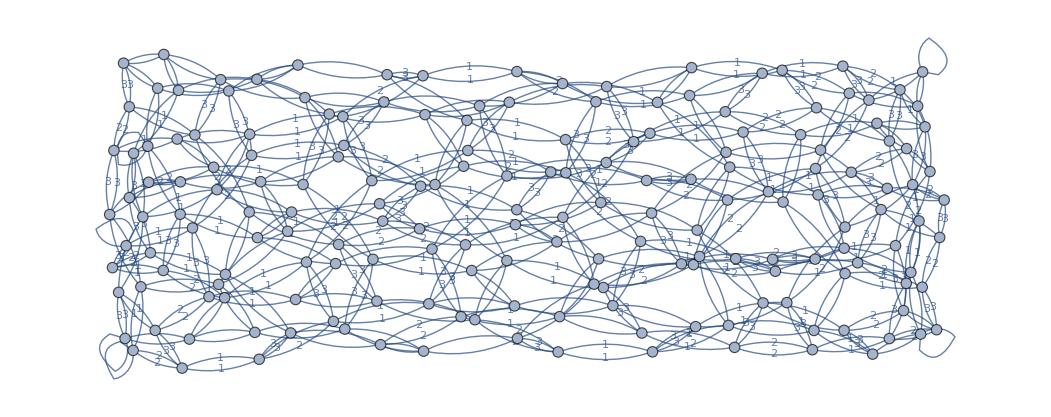

```mathematica
G = {{5,4,2},{103,102,2},{199,200,2},{40,39,2},{61,60,1},{334,113,3},{25,24,2},{334,63,2},{225,62,3},{105,106,1},{97,98,1},{42,43,1},{32,21,3},{147,193,3},{131,132,2},{325,445,2},{116,117,2},{55,54,1},{8,19,2},{134,133,2},{652,651,1},{110,111,2},{32,28,2},{775,776,2},{52,137,2},{93,495,2},{11,10,2},{94,223,3},{495,93,2},{19,8,2},{149,150,2},{38,37,2},{28,29,1},{209,23,3},{7,8,1},{107,106,2},{9,8,3},{224,225,1},{13,12,2},{492,206,3},{28,32,2},{384,385,1},{385,779,2},{225,224,1},{651,652,1},{109,110,1},{199,40,3},{328,107,3},{493,494,2},{106,156,3},{201,849,3},{853,774,2},{135,136,2},{274,160,1},{157,156,1},{10,137,3},{94,93,1},{20,21,2},{190,19,3},{97,850,3},{118,57,2},{222,852,3},{3,3,3},{113,112,2},{442,775,3},{27,491,1},{382,134,3},{12,13,2},{95,96,1},{202,56,3},{23,209,3},{491,242,3},{132,131,2},{153,152,1},{241,445,3},{42,58,2},{328,327,1},{96,95,1},{326,327,2},{137,10,3},{265,264,1},{493,45,3},{131,13,3},{148,43,3},{243,652,3},{53,52,1},{264,263,2},{5,38,3},{131,655,1},{776,775,2},{262,157,3},{778,151,3},{443,444,2},{6,7,2},{104,26,3},{146,222,2},{34,35,1},{650,651,2},{56,202,3},{194,172,1},{330,240,3},{103,104,1},{191,54,3},{60,61,1},{97,96,2},{37,38,2},{99,693,3},{106,107,2},{134,135,1},{332,331,1},{272,273,1},{441,197,1},{41,694,2},{133,134,2},{223,224,2},{57,56,1},{444,34,3},{272,192,3},{147,146,1},{10,11,2},{6,226,3},{494,776,3},{209,208,1},{654,655,2},{241,242,2},{443,101,3},{98,495,3},{263,262,1},{43,42,1},{99,100,1},{105,104,2},{777,653,3},{63,62,1},{274,273,2},{208,136,3},{382,262,2},{62,61,2},{851,851,3},{200,95,3},{651,650,2},{156,106,3},{203,7,3},{38,5,3},{134,382,3},{114,441,3},{193,147,3},{93,94,1},{53,244,3},{331,385,3},{206,205,2},{151,150,1},{148,149,1},{112,113,2},{777,778,2},{779,159,3},{849,201,3},{104,105,2},{202,203,1},{24,2,3},{224,223,2},{262,263,1},{327,384,3},{384,327,3},{693,694,1},{223,94,3},{495,494,1},{9,10,1},{103,654,3},{109,108,2},{207,206,1},{107,328,3},{331,332,1},{98,99,2},{774,853,2},{56,57,1},{22,21,1},{156,155,2},{207,655,3},{226,225,2},{851,850,1},{199,198,1},{652,653,2},{158,105,3},{192,272,3},{849,650,1},{155,210,3},{210,209,2},{2,13,1},{159,158,1},{152,153,1},{694,41,2},{37,93,3},{58,59,1},{3,172,2},{327,326,2},{95,94,2},{193,192,1},{383,384,2},{25,383,3},{118,39,3},{445,444,1},{108,109,2},{206,207,1},{113,334,3},{444,443,2},{36,651,3},{850,851,1},{653,777,3},{149,148,1},{40,199,3},{102,103,2},{172,3,2},{325,264,3},{26,25,1},{160,159,2},{158,159,1},{203,202,1},{94,95,2},{60,59,2},{116,4,3},{693,272,2},{101,443,3},{156,157,1},{206,492,3},{62,63,1},{273,274,2},{493,492,1},{210,155,3},{135,134,1},{13,131,3},{99,98,2},{20,110,3},{96,97,2},{146,117,3},{33,34,2},{20,19,1},{779,778,1},{110,109,1},{242,491,3},{39,118,3},{226,244,1},{13,2,1},{650,44,3},{334,333,1},{654,103,3},{237,133,3},{208,207,2},{225,226,2},{775,442,3},{243,242,1},{61,774,3},{849,850,2},{198,224,3},{326,325,1},{204,149,3},{148,147,2},{265,190,2},{100,150,3},{443,442,1},{6,5,1},{445,325,2},{4,5,2},{202,201,2},{331,330,2},{56,55,2},{110,20,3},{45,44,1},{333,334,1},{57,58,3},{34,444,3},{100,101,2},{39,38,1},{58,57,3},{24,23,1},{114,113,1},{222,146,2},{46,328,2},{59,58,1},{132,29,3},{149,204,3},{136,208,3},{46,1,3},{326,108,3},{327,328,1},{445,241,3},{45,9,2},{779,385,2},{441,114,3},{62,225,3},{150,151,1},{444,445,1},{494,493,2},{44,45,1},{10,9,1},{383,25,3},{154,12,3},{12,154,3},{204,205,1},{264,325,3},{654,653,1},{655,131,1},{198,197,2},{22,236,3},{19,190,3},{237,236,1},{150,100,3},{153,263,3},{332,333,2},{244,226,1},{118,117,1},{850,97,3},{236,240,2},{158,157,2},{151,152,2},{201,200,1},{385,384,1},{52,53,1},{200,199,2},{152,151,2},{190,191,1},{172,59,3},{33,52,3},{60,96,3},{240,236,2},{491,27,1},{154,155,1},{778,779,1},{155,154,1},{853,694,3},{205,274,3},{117,146,3},{694,693,1},{385,331,3},{112,111,1},{263,264,2},{850,849,2},{159,779,3},{208,209,1},{207,208,2},{236,22,3},{1,29,2},{23,24,1},{325,326,1},{852,853,1},{22,23,2},{494,495,1},{157,262,3},{241,240,1},{205,204,1},{98,97,1},{55,56,2},{35,34,1},{193,194,2},{262,382,2},{190,265,2},{54,53,2},{330,46,1},{137,136,1},{333,265,3},{774,61,3},{26,104,3},{330,331,2},{263,153,3},{116,115,1},{693,99,3},{191,190,1},{383,382,1},{57,118,2},{775,774,1},{29,1,2},{1,1,1},{265,333,3},{61,62,2},{27,26,2},{851,852,2},{105,158,3},{242,243,1},{204,203,2},{29,132,3},{240,330,3},{137,52,2},{102,101,1},{198,199,1},{8,7,1},{96,60,3},{46,330,1},{333,332,2},{136,135,2},{21,22,1},{776,494,3},{112,273,3},{172,194,1},{651,36,3},{52,33,3},{9,45,2},{41,40,1},{273,272,1},{224,198,3},{852,222,3},{26,27,2},{442,441,2},{243,244,2},{1,46,3},{774,775,1},{54,55,1},{108,326,3},{192,193,1},{244,243,2},{33,32,1},{150,149,2},{108,107,1},{133,237,3},{237,237,2},{203,204,2},{44,43,2},{43,148,3},{495,98,3},{160,274,1},{151,778,3},{197,198,2},{135,109,3},{23,22,2},{106,105,1},{226,6,3},{12,11,1},{5,6,1},{93,37,3},{40,41,1},{42,41,3},{157,158,2},{25,26,1},{35,63,3},{240,241,1},{200,201,1},{115,116,1},{63,35,3},{4,3,1},{114,115,2},{492,493,1},{194,193,2},{273,112,3},{117,118,1},{45,493,3},{37,36,1},{244,53,3},{154,153,2},{147,148,2},{2,2,2},{53,54,2},{152,111,3},{778,777,2},{28,27,3},{11,12,1},{653,652,2},{111,110,2},{101,102,1},{11,160,3},{210,210,1},{109,135,3},{652,243,3},{853,852,1},{382,383,1},{223,222,1},{274,205,3},{115,55,3},{852,851,2},{655,654,2},{332,102,3},{491,492,2},{194,197,3},{4,116,3},{39,40,2},{24,25,2},{201,202,2},{2,24,3},{153,154,2},{19,20,1},{197,194,3},{59,60,2},{236,237,1},{136,137,1},{160,11,3},{95,200,3},{100,99,1},{63,334,2},{155,156,2},{197,441,1},{36,35,2},{113,114,1},{442,443,1},{441,442,2},{222,223,1},{209,210,2},{133,132,1},{32,33,1},{107,108,1},{102,332,3},{111,152,3},{8,9,3},{777,776,1},{59,172,3},{43,44,2},{242,241,2},{44,650,3},{272,693,2},{7,203,3},{35,36,2},{29,28,1},{115,114,2},{41,42,3},{21,20,2},{55,115,3},{104,103,1},{3,4,1},{492,491,2},{159,160,2},{132,133,1},{21,32,3},{38,39,1},{694,853,3},{655,207,3},{191,192,2},{117,116,2},{328,46,2},{54,191,3},{192,191,2},{36,37,1},{653,654,1},{264,265,1},{111,112,1},{205,206,2},{101,100,2},{27,28,3},{7,6,2},{776,777,1},{146,147,1},{384,383,2},{34,33,2},{650,849,1},{58,42,2}}

GraphPlot[MakeGraph[G]]
```

{{128,129,2},{9,35,3},{5,4,2},{43,44,1},{39,40,1},{6,23,2},{23,85,1},{127,128,1},{52,51,1},{186,185,1},{129,128,2},{42,41,1},{191,18,3},{44,3,2},{47,37,3},{135,190,1},{70,69,1},{144,128,3},{5,6,1},{23,19,3},{191,190,2},{36,190,3},{148,149,1},{2,38,3},{78,66,3},{10,9,1},{192,301,2},{54,4,3},{36,35,1},{4,3,1},{85,149,2},{70,43,3},{16,17,3},{185,302,3},{135,5,3},{147,65,2},{10,1,2},{44,127,3},{65,147,2},{69,127,2},{77,41,3},{54,53,1},{192,191,1},{66,78,3},{51,50,3},{48,145,3},{53,52,2},{81,81,1},{185,148,2},{145,144,1},{9,10,1},{6,7,3},{145,48,3},{301,42,3},{8,9,2},{2,2,2},{7,8,1},{302,185,3},{301,192,2},{85,23,1},{37,38,1},{5,135,3},{8,65,3},{146,145,2},{36,37,2},{16,15,1},{41,77,3},{35,36,1},{18,19,2},{41,40,2},{81,15,3},{42,301,3},{40,39,1},{47,24,2},{192,129,3},{77,302,2},{39,38,2},{15,7,2},{127,44,3},{1,24,3},{65,8,3},{70,17,2},{81,50,2},{18,191,3},{191,192,1},{3,44,2},{146,53,3},{129,24,1},{3,3,3},{39,149,3},{65,66,1},{48,49,2},{4,54,3},{148,147,3},{35,54,2},{50,81,2},{47,48,1},{42,43,2},{38,39,2},{144,186,2},{185,186,1},{190,36,3},{302,301,1},{149,148,1},{40,41,2},{38,37,1},{50,51,3},{186,144,2},{53,54,1},{19,18,2},{16,78,2},{7,6,3},{9,8,2},{18,17,1},{1,10,2},{37,47,3},{44,43,1},{301,302,1},{51,52,1},{69,52,3},{10,186,3},{15,81,3},{23,6,2},{77,78,1},{43,42,2},{24,47,2},{38,2,3},{37,36,2},{43,70,3},{147,148,3},{85,49,3},{129,192,3},{41,42,1},{52,53,2},{19,23,3},{50,49,1},{69,70,1},{148,185,2},{19,2,1},{1,1,1},{48,47,1},{35,9,3},{144,145,1},{149,39,3},{78,77,1},{24,1,3},{3,4,1},{52,69,3},{49,85,3},{66,65,1},{147,146,1},{49,48,2},{8,7,1},{128,127,1},{149,85,2},{40,40,3},{6,5,1},{17,18,1},{4,5,2},{78,16,2},{17,70,2},{7,15,2},{127,69,2},{66,51,2},{302,77,2},{49,50,1},{24,129,1},{54,35,2},{190,135,1},{2,19,1},{146,147,1},{145,146,2},{15,16,1},{135,135,2},{190,191,2},{17,16,3},{51,66,2},{128,144,3},{53,146,3},{186,10,3}}

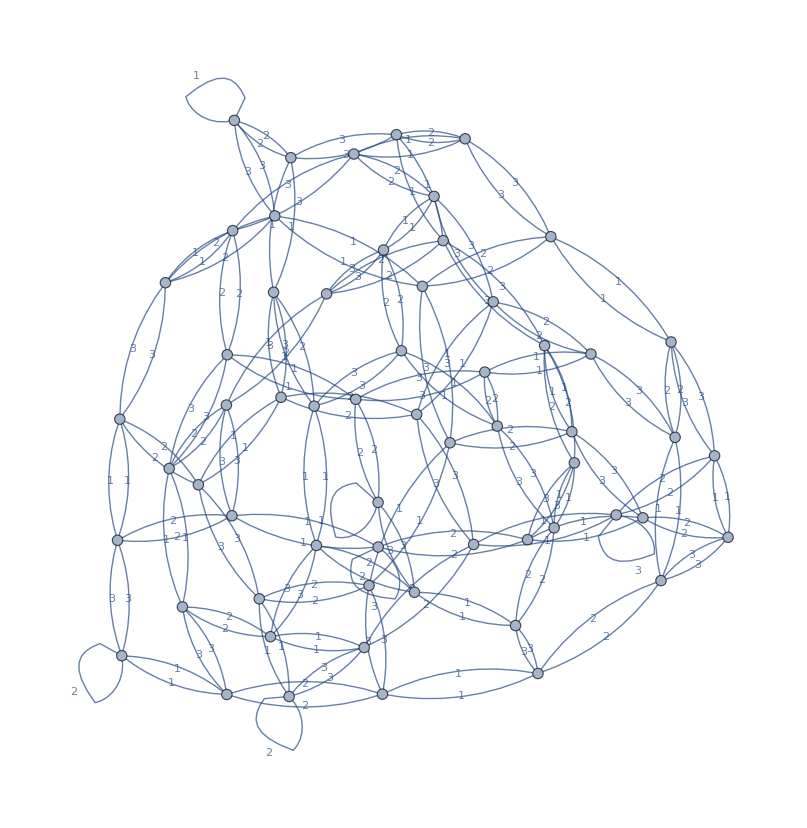

```mathematica
G = {{128,129,2},{9,35,3},{5,4,2},{43,44,1},{39,40,1},{6,23,2},{23,85,1},{127,128,1},{52,51,1},{186,185,1},{129,128,2},{42,41,1},{191,18,3},{44,3,2},{47,37,3},{135,190,1},{70,69,1},{144,128,3},{5,6,1},{23,19,3},{191,190,2},{36,190,3},{148,149,1},{2,38,3},{78,66,3},{10,9,1},{192,301,2},{54,4,3},{36,35,1},{4,3,1},{85,149,2},{70,43,3},{16,17,3},{185,302,3},{135,5,3},{147,65,2},{10,1,2},{44,127,3},{65,147,2},{69,127,2},{77,41,3},{54,53,1},{192,191,1},{66,78,3},{51,50,3},{48,145,3},{53,52,2},{81,81,1},{185,148,2},{145,144,1},{9,10,1},{6,7,3},{145,48,3},{301,42,3},{8,9,2},{2,2,2},{7,8,1},{302,185,3},{301,192,2},{85,23,1},{37,38,1},{5,135,3},{8,65,3},{146,145,2},{36,37,2},{16,15,1},{41,77,3},{35,36,1},{18,19,2},{41,40,2},{81,15,3},{42,301,3},{40,39,1},{47,24,2},{192,129,3},{77,302,2},{39,38,2},{15,7,2},{127,44,3},{1,24,3},{65,8,3},{70,17,2},{81,50,2},{18,191,3},{191,192,1},{3,44,2},{146,53,3},{129,24,1},{3,3,3},{39,149,3},{65,66,1},{48,49,2},{4,54,3},{148,147,3},{35,54,2},{50,81,2},{47,48,1},{42,43,2},{38,39,2},{144,186,2},{185,186,1},{190,36,3},{302,301,1},{149,148,1},{40,41,2},{38,37,1},{50,51,3},{186,144,2},{53,54,1},{19,18,2},{16,78,2},{7,6,3},{9,8,2},{18,17,1},{1,10,2},{37,47,3},{44,43,1},{301,302,1},{51,52,1},{69,52,3},{10,186,3},{15,81,3},{23,6,2},{77,78,1},{43,42,2},{24,47,2},{38,2,3},{37,36,2},{43,70,3},{147,148,3},{85,49,3},{129,192,3},{41,42,1},{52,53,2},{19,23,3},{50,49,1},{69,70,1},{148,185,2},{19,2,1},{1,1,1},{48,47,1},{35,9,3},{144,145,1},{149,39,3},{78,77,1},{24,1,3},{3,4,1},{52,69,3},{49,85,3},{66,65,1},{147,146,1},{49,48,2},{8,7,1},{128,127,1},{149,85,2},{40,40,3},{6,5,1},{17,18,1},{4,5,2},{78,16,2},{17,70,2},{7,15,2},{127,69,2},{66,51,2},{302,77,2},{49,50,1},{24,129,1},{54,35,2},{190,135,1},{2,19,1},{146,147,1},{145,146,2},{15,16,1},{135,135,2},{190,191,2},{17,16,3},{51,66,2},{128,144,3},{53,146,3},{186,10,3}}
GraphPlot[MakeGraph[G]]
```

{{266,207,3},{14,13,2},{155,119,2},{265,266,1},{77,10,2},{119,4,3},{13,14,2},{156,157,2},{4,1,2},{93,94,1},{31,2,3},{157,156,2},{42,43,1},{118,42,3},{41,42,2},{45,76,3},{28,47,2},{114,114,1},{76,77,1},{40,41,1},{44,45,1},{311,11,3},{46,45,2},{159,160,1},{158,72,2},{44,73,2},{152,37,3},{73,93,3},{156,41,3},{37,3,2},{94,266,2},{6,7,1},{10,11,1},{311,362,1},{9,8,1},{10,9,3},{29,30,2},{16,15,2},{47,46,1},{28,29,1},{8,114,3},{37,36,1},{3,13,1},{312,313,1},{2,2,2},{311,312,2},{93,73,3},{72,6,3},{46,157,3},{45,46,2},{76,152,2},{41,156,3},{12,16,3},{76,45,3},{9,10,3},{5,4,1},{29,312,3},{31,30,1},{114,43,2},{362,265,2},{43,44,3},{93,9,2},{72,158,2},{207,119,1},{13,3,1},{160,32,3},{119,207,1},{42,118,3},{1,24,3},{94,93,1},{313,14,3},{160,118,2},{362,311,1},{24,40,2},{30,29,2},{42,41,2},{157,158,1},{4,5,1},{159,158,3},{3,3,3},{94,34,3},{46,47,1},{207,159,2},{33,33,3},{119,155,2},{34,94,3},{114,8,3},{151,150,2},{8,7,2},{207,266,3},{31,32,2},{7,6,1},{11,10,1},{313,312,1},{6,5,2},{30,31,1},{362,150,3},{32,31,2},{1,4,2},{150,24,1},{36,35,2},{7,15,3},{35,34,1},{159,207,2},{32,160,3},{6,72,3},{8,9,1},{73,44,2},{34,35,1},{151,155,3},{152,151,1},{16,118,1},{265,35,3},{14,313,3},{312,311,2},{32,33,1},{15,16,2},{2,31,3},{37,152,3},{14,15,1},{5,28,3},{7,8,2},{118,16,1},{33,34,2},{44,43,3},{47,28,2},{43,114,2},{150,362,3},{16,12,3},{40,24,2},{2,12,1},{9,93,2},{35,36,2},{1,1,1},{118,160,2},{150,151,2},{157,46,3},{29,28,1},{77,36,3},{12,11,2},{5,6,2},{24,1,3},{28,5,3},{155,151,3},{24,150,1},{4,119,3},{15,7,3},{47,13,3},{265,362,2},{152,76,2},{313,313,2},{266,265,1},{158,157,1},{72,73,1},{12,2,1},{151,152,1},{312,29,3},{10,77,2},{30,40,3},{155,156,1},{77,76,1},{156,155,1},{160,159,1},{11,311,3},{36,37,1},{35,265,3},{158,159,3},{15,14,1},{41,40,1},{45,44,1},{266,94,2},{11,12,2},{13,47,3},{43,42,1},{36,77,3},{34,33,2},{3,37,2},{73,72,1},{33,32,1},{40,30,3}}

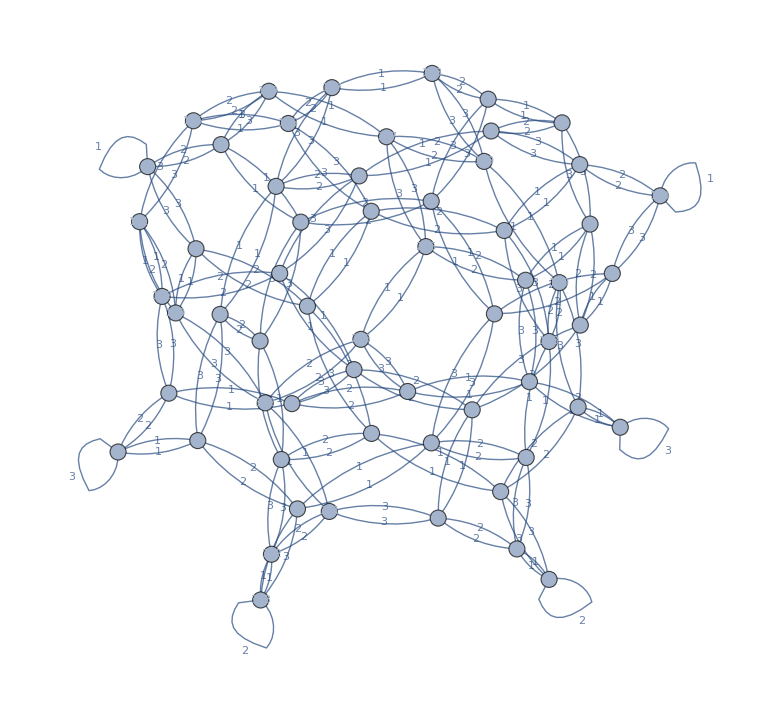

```mathematica
G = {{266,207,3},{14,13,2},{155,119,2},{265,266,1},{77,10,2},{119,4,3},{13,14,2},{156,157,2},{4,1,2},{93,94,1},{31,2,3},{157,156,2},{42,43,1},{118,42,3},{41,42,2},{45,76,3},{28,47,2},{114,114,1},{76,77,1},{40,41,1},{44,45,1},{311,11,3},{46,45,2},{159,160,1},{158,72,2},{44,73,2},{152,37,3},{73,93,3},{156,41,3},{37,3,2},{94,266,2},{6,7,1},{10,11,1},{311,362,1},{9,8,1},{10,9,3},{29,30,2},{16,15,2},{47,46,1},{28,29,1},{8,114,3},{37,36,1},{3,13,1},{312,313,1},{2,2,2},{311,312,2},{93,73,3},{72,6,3},{46,157,3},{45,46,2},{76,152,2},{41,156,3},{12,16,3},{76,45,3},{9,10,3},{5,4,1},{29,312,3},{31,30,1},{114,43,2},{362,265,2},{43,44,3},{93,9,2},{72,158,2},{207,119,1},{13,3,1},{160,32,3},{119,207,1},{42,118,3},{1,24,3},{94,93,1},{313,14,3},{160,118,2},{362,311,1},{24,40,2},{30,29,2},{42,41,2},{157,158,1},{4,5,1},{159,158,3},{3,3,3},{94,34,3},{46,47,1},{207,159,2},{33,33,3},{119,155,2},{34,94,3},{114,8,3},{151,150,2},{8,7,2},{207,266,3},{31,32,2},{7,6,1},{11,10,1},{313,312,1},{6,5,2},{30,31,1},{362,150,3},{32,31,2},{1,4,2},{150,24,1},{36,35,2},{7,15,3},{35,34,1},{159,207,2},{32,160,3},{6,72,3},{8,9,1},{73,44,2},{34,35,1},{151,155,3},{152,151,1},{16,118,1},{265,35,3},{14,313,3},{312,311,2},{32,33,1},{15,16,2},{2,31,3},{37,152,3},{14,15,1},{5,28,3},{7,8,2},{118,16,1},{33,34,2},{44,43,3},{47,28,2},{43,114,2},{150,362,3},{16,12,3},{40,24,2},{2,12,1},{9,93,2},{35,36,2},{1,1,1},{118,160,2},{150,151,2},{157,46,3},{29,28,1},{77,36,3},{12,11,2},{5,6,2},{24,1,3},{28,5,3},{155,151,3},{24,150,1},{4,119,3},{15,7,3},{47,13,3},{265,362,2},{152,76,2},{313,313,2},{266,265,1},{158,157,1},{72,73,1},{12,2,1},{151,152,1},{312,29,3},{10,77,2},{30,40,3},{155,156,1},{77,76,1},{156,155,1},{160,159,1},{11,311,3},{36,37,1},{35,265,3},{158,159,3},{15,14,1},{41,40,1},{45,44,1},{266,94,2},{11,12,2},{13,47,3},{43,42,1},{36,77,3},{34,33,2},{3,37,2},{73,72,1},{33,32,1},{40,30,3}}

GraphPlot[MakeGraph[G], VertexLabels->Placed[Automatic,Center],VertexSize->.75]
```

{{61,56,1},{216,217,1},{183,123,2},{123,183,2},{97,96,1},{10,83,3},{83,10,3},{4,1,2},{104,21,1},{12,13,1},{27,26,1},{52,67,2},{70,37,3},{70,69,1},{56,36,2},{56,61,1},{202,9,3},{2,11,1},{83,26,2},{70,97,2},{55,54,1},{95,67,3},{21,8,2},{22,213,2},{213,212,1},{217,216,1},{131,54,3},{14,124,2},{95,96,2},{213,28,3},{6,7,1},{8,7,3},{94,95,1},{132,104,3},{9,8,1},{129,131,2},{21,11,3},{3,35,2},{216,182,2},{29,30,2},{36,35,3},{13,61,2},{38,37,2},{30,94,3},{28,29,1},{212,69,3},{37,36,1},{182,33,3},{27,28,2},{202,218,1},{53,54,2},{32,123,3},{26,27,1},{132,212,2},{2,2,2},{10,3,1},{96,97,1},{52,53,1},{68,192,3},{129,15,3},{56,55,3},{38,216,3},{5,4,1},{31,30,1},{27,218,3},{22,38,1},{61,34,3},{26,83,2},{7,8,3},{6,52,3},{69,68,2},{182,183,1},{97,70,2},{15,7,2},{212,132,2},{68,67,1},{11,2,1},{35,36,3},{36,56,2},{183,182,1},{213,22,2},{217,12,3},{69,212,3},{67,68,1},{15,129,3},{30,29,2},{4,5,1},{67,95,3},{37,70,3},{3,3,3},{53,124,3},{35,3,2},{202,202,2},{218,27,3},{192,68,3},{9,202,3},{192,83,1},{31,31,3},{31,32,2},{7,6,1},{6,5,2},{30,31,1},{218,202,1},{212,213,1},{123,124,1},{53,52,1},{32,31,2},{1,4,2},{33,182,3},{124,123,1},{35,34,1},{83,192,1},{192,55,2},{182,216,2},{123,32,3},{104,132,3},{8,9,1},{21,104,1},{61,13,2},{34,35,1},{11,21,3},{55,192,2},{13,12,1},{54,53,2},{32,33,1},{22,1,3},{14,15,1},{9,10,2},{54,131,3},{94,30,3},{67,52,2},{14,13,3},{33,34,2},{131,132,1},{37,38,2},{131,129,2},{13,14,3},{95,94,1},{69,70,1},{1,1,1},{12,217,3},{38,22,1},{183,96,3},{29,28,1},{12,11,2},{5,6,2},{129,129,1},{10,9,2},{97,4,3},{29,2,3},{94,104,2},{132,131,1},{68,69,2},{4,97,3},{26,5,3},{3,10,1},{124,14,2},{28,27,2},{217,218,2},{2,29,3},{7,15,2},{124,53,3},{8,21,2},{96,183,3},{36,37,1},{15,14,1},{1,22,3},{5,26,3},{96,95,2},{28,213,3},{11,12,2},{104,94,2},{54,55,1},{216,38,3},{218,217,2},{34,33,2},{52,6,3},{55,56,3},{33,32,1},{34,61,3}}

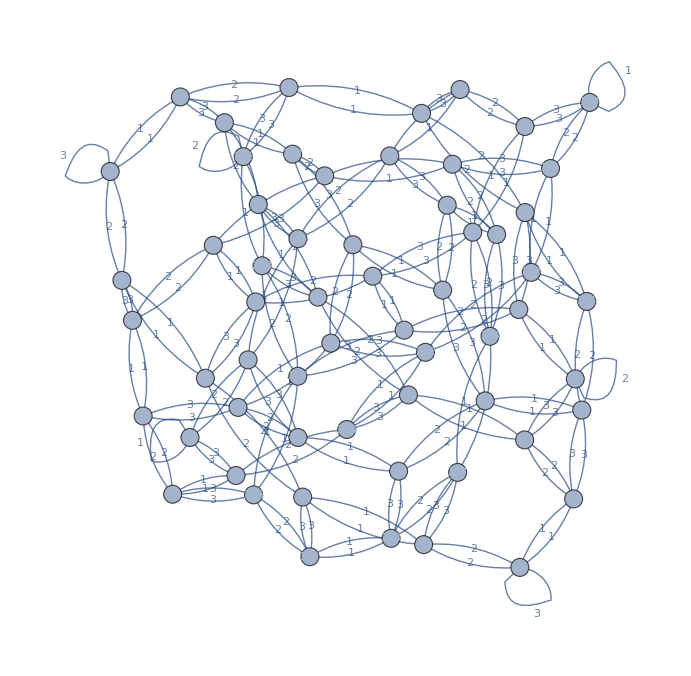

```mathematica
(*k = -2 1,1,1*)
G = {{61,56,1},{216,217,1},{183,123,2},{123,183,2},{97,96,1},{10,83,3},{83,10,3},{4,1,2},{104,21,1},{12,13,1},{27,26,1},{52,67,2},{70,37,3},{70,69,1},{56,36,2},{56,61,1},{202,9,3},{2,11,1},{83,26,2},{70,97,2},{55,54,1},{95,67,3},{21,8,2},{22,213,2},{213,212,1},{217,216,1},{131,54,3},{14,124,2},{95,96,2},{213,28,3},{6,7,1},{8,7,3},{94,95,1},{132,104,3},{9,8,1},{129,131,2},{21,11,3},{3,35,2},{216,182,2},{29,30,2},{36,35,3},{13,61,2},{38,37,2},{30,94,3},{28,29,1},{212,69,3},{37,36,1},{182,33,3},{27,28,2},{202,218,1},{53,54,2},{32,123,3},{26,27,1},{132,212,2},{2,2,2},{10,3,1},{96,97,1},{52,53,1},{68,192,3},{129,15,3},{56,55,3},{38,216,3},{5,4,1},{31,30,1},{27,218,3},{22,38,1},{61,34,3},{26,83,2},{7,8,3},{6,52,3},{69,68,2},{182,183,1},{97,70,2},{15,7,2},{212,132,2},{68,67,1},{11,2,1},{35,36,3},{36,56,2},{183,182,1},{213,22,2},{217,12,3},{69,212,3},{67,68,1},{15,129,3},{30,29,2},{4,5,1},{67,95,3},{37,70,3},{3,3,3},{53,124,3},{35,3,2},{202,202,2},{218,27,3},{192,68,3},{9,202,3},{192,83,1},{31,31,3},{31,32,2},{7,6,1},{6,5,2},{30,31,1},{218,202,1},{212,213,1},{123,124,1},{53,52,1},{32,31,2},{1,4,2},{33,182,3},{124,123,1},{35,34,1},{83,192,1},{192,55,2},{182,216,2},{123,32,3},{104,132,3},{8,9,1},{21,104,1},{61,13,2},{34,35,1},{11,21,3},{55,192,2},{13,12,1},{54,53,2},{32,33,1},{22,1,3},{14,15,1},{9,10,2},{54,131,3},{94,30,3},{67,52,2},{14,13,3},{33,34,2},{131,132,1},{37,38,2},{131,129,2},{13,14,3},{95,94,1},{69,70,1},{1,1,1},{12,217,3},{38,22,1},{183,96,3},{29,28,1},{12,11,2},{5,6,2},{129,129,1},{10,9,2},{97,4,3},{29,2,3},{94,104,2},{132,131,1},{68,69,2},{4,97,3},{26,5,3},{3,10,1},{124,14,2},{28,27,2},{217,218,2},{2,29,3},{7,15,2},{124,53,3},{8,21,2},{96,183,3},{36,37,1},{15,14,1},{1,22,3},{5,26,3},{96,95,2},{28,213,3},{11,12,2},{104,94,2},{54,55,1},{216,38,3},{218,217,2},{34,33,2},{52,6,3},{55,56,3},{33,32,1},{34,61,3}}

GraphPlot[MakeGraph[G], VertexLabels->Placed[Automatic,Center],VertexSize->.75]
```